```mathematica
α=2.;u0=1.*10^-8;
k:=√(2e);ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
```

```mathematica
δ50Lepage={-0.000421343353,-0.133227246,-1.319383451,-0.900186195,-0.146570028,-0.654835316,1.232867297,-0.579619620,-1.156444634,-0.106466466,-1.457426179,1.160634967};
```

```mathematica
δ[V_][r1_,n_]:=
Module[{r2=u0,sol,δr,δs,δ50r,ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1},jder,nder,β},
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];
β:=r1 u'[r1]/u[r1]-1;
δ50r=Table[
e=ee[[i]];
sol=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs=FindRoot[Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->30,AccuracyGoal->Infinity,PrecisionGoal->20];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&];
δr,{i,1,n}]
]
```

```mathematica
SetSharedFunction[ParallelSow];
ParallelSow[expr_,condition_]:=Sow[expr,condition];
```

```mathematica
NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&][50,12]-δ[-1/#&][50,12])
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.616853) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-15.5631) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==0.0432091) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

{0.000467719350306150591136829009,0.14840866458052095836354309076,1.5523348215791700423279350862,-1.1735632941796765351818753257,1.4235922542965249283991753159,0.91557277230108624301479965993,1.2056883456083858986630337324,0.947858251732200259905508544606,0.9759772801790736266176077074,1.01771176780138454079033976819,0.93914936562525876520565477819,0.8855634222191990030470658803}

```mathematica
Table[
δ[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&][r1,12]-δ[-1/#&][r1,12],{r1,1,100}];
N[%,6]//TableForm
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.0468484) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.0812267) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.12433) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

0.000019696 | 0.00622821 | 0.0620563 | 0.106706 | 0.160687 | 0.190055 | 0.308296 | 0.420505 | 0.467059 | 0.569618 | -2.55871 | -2.5665
0.0000226601 | 0.0071657 | 0.0716103 | 0.123869 | 0.188714 | 0.225108 | 0.384725 | 0.571848 | 0.669299 | 0.998658 | 1.10113 | -2.11546
-0.000061906 | -0.0195751 | -0.194462 | -0.332528 | -0.496033 | -0.583267 | -0.927043 | 1.86836 | 1.69771 | 1.10089 | 0.79423 | 0.78298
0.000137596 | 0.0434655 | 0.395263 | 0.588882 | 0.725647 | 0.76843 | -2.32356 | -2.3627 | 0.754379 | 0.768288 | 1.00889 | 0.964431
0.0000285089 | 0.00901464 | 0.0894975 | 0.152847 | 0.227432 | 0.266947 | 0.420814 | -2.55892 | 0.676525 | 1.12853 | 0.896529 | 0.829435
0.0000355363 | 0.0112378 | 0.112554 | 0.195589 | 0.300829 | 0.361494 | 0.649036 | -2.11364 | -1.93823 | 1.08186 | 0.915818 | 0.944311
0.000244984 | 0.0773588 | 0.686403 | 1.0115 | 1.26727 | 1.36738 | 1.6029 | -1.56681 | -1.71104 | 0.847987 | 0.977663 | 0.842876
-0.000101241 | -0.0320073 | -0.312824 | -0.520693 | -0.748825 | -0.865738 | 1.78176 | 1.18853 | 0.963899 | 1.01538 | 0.871122 | 0.935404
-0.000200203 | -0.0632906 | -0.614936 | -1.01113 | -1.41607 | -1.60192 | 1.00325 | 0.761222 | 0.756393 | -2.01579 | 0.990299 | 0.850369
0.0000989959 | 0.0312745 | 0.285783 | 0.426414 | -2.61907 | -2.5905 | 0.602198 | 0.735232 | 0.912121 | -2.2141 | 0.895926 | 0.92784
0.0000449271 | 0.0142036 | 0.138686 | 0.23006 | 0.327833 | -2.76518 | 0.588068 | 1.02012 | 1.25605 | -2.21424 | 0.9367 | 0.858028
0.0000417861 | 0.0132136 | 0.131923 | 0.228346 | 0.35152 | -2.7162 | 0.856497 | 1.37661 | 1.28057 | -2.05015 | 0.953536 | 0.918819
0.0000631596 | 0.0199764 | 0.203404 | 0.365438 | 0.598888 | -2.3916 | -1.73469 | 1.30842 | 0.9927 | -2.11 | 0.894067 | 0.867329
0.000251891 | 0.079598 | 0.745595 | 1.15839 | 1.49732 | -1.52542 | -1.49703 | 0.975639 | 0.83374 | -2.22637 | 0.970227 | 0.908159
-0.000199029 | -0.0628299 | -0.545433 | 2.35464 | 2.15003 | -1.10116 | -1.81068 | 0.799428 | 0.907658 | -2.14639 | 0.908884 | 0.877995
-0.000136828 | -0.0432644 | -0.429299 | -0.741564 | 1.98487 | 1.73271 | -2.25541 | 0.845074 | 1.13664 | -2.05961 | 0.931743 | 0.896915
-0.000346416 | -0.109456 | -1.0164 | -1.56238 | 1.13534 | 0.970978 | 0.685375 | 1.07111 | 1.25373 | -2.1593 | 0.951668 | 0.888823
0.000187775 | 0.0591818 | 0.454581 | -2.57905 | 0.581518 | 0.578132 | 0.686253 | 1.29389 | 1.10818 | -2.20655 | 0.902313 | 0.886652
0.0000747553 | 0.0236181 | 0.217345 | -2.8118 | 0.424367 | 0.470597 | 0.86278 | -1.88228 | 0.922505 | -2.11131 | 0.958129 | 0.898176
0.000055375 | 0.017505 | 0.169697 | -2.86058 | 0.414791 | 0.501145 | 1.20284 | -2.10573 | 0.88316 | -2.08556 | 0.92023 | 0.878906
0.000055712 | 0.0176182 | 0.177083 | -2.82767 | 0.522866 | 0.681381 | 1.47866 | -2.26997 | 0.999774 | 0.962164 | 0.924629 | 0.904489
0.0000737142 | 0.02332 | 0.243279 | -2.67927 | 0.848111 | 1.1184 | 1.44872 | -2.28129 | 1.16763 | 0.958153 | 0.952662 | 0.874776
0.000146753 | 0.0464452 | 0.500577 | -2.18023 | -1.64442 | -1.47591 | 1.1682 | -2.15086 | 1.19444 | 1.04398 | 0.907984 | 0.906759
0.00920468 | 1.26471 | 1.79243 | -1.21503 | -1.19678 | -1.28113 | 0.889625 | -1.9606 | 1.05807 | 1.03281 | 0.948024 | 0.87467
-0.000223243 | -0.0704282 | -0.589568 | 2.28772 | -1.205 | -1.48796 | 0.754151 | -1.88504 | -2.21161 | 0.956389 | 0.930178 | 0.90489
-0.000172653 | -0.0545841 | -0.539389 | 2.18044 | -1.62231 | -1.97544 | 0.753461 | -1.99513 | -2.22198 | 0.977366 | -2.22267 | 0.878203
-0.000265011 | -0.0838657 | -0.891174 | 1.54273 | 0.945886 | 0.775121 | 0.875766 | -2.16434 | -2.11729 | 1.04656 | -2.18941 | 0.899753
0.00145451 | 0.422145 | -2.21046 | 0.768503 | 0.62699 | 0.595814 | 1.10639 | -2.2539 | -1.98985 | 1.01554 | -2.22722 | 0.884247
0.000162762 | 0.0512777 | -2.75909 | 0.464352 | 0.504031 | 0.546823 | 1.3384 | -2.22602 | -1.97693 | 0.957246 | -2.20312 | 0.892941
0.0000904652 | 0.0285624 | 0.249632 | 0.362189 | 0.484713 | 0.591705 | 1.41035 | -2.1005 | -2.08594 | 0.99167 | -2.20326 | 0.891154
0.000070485 | 0.0222732 | 0.209871 | 0.342405 | 0.548752 | 0.745069 | 1.28183 | 1.1809 | -2.19111 | 1.04403 | -2.22564 | 0.886319
0.0000671752 | 0.0212401 | 0.211807 | 0.382862 | 0.726411 | 1.04749 | 1.05684 | 1.2135 | -2.20418 | 1.0035 | -2.1926 | 0.897123
0.0000760673 | 0.0240655 | 0.253791 | 0.509749 | 1.08107 | 1.44019 | 0.877112 | 1.11423 | -2.12225 | 0.960937 | -2.21961 | 0.881532
0.000104921 | 0.0332166 | 0.373895 | 0.825257 | 1.54015 | 1.69199 | 0.797073 | 0.981593 | -2.01487 | 1.00176 | -2.21166 | 0.900662
0.000201049 | 0.0637017 | 0.753126 | -1.68092 | 1.81547 | 1.6909 | 0.814763 | 0.912955 | -1.99031 | 1.03948 | -2.19784 | 0.879624
0.00189886 | 0.553016 | 1.81247 | -1.14085 | 1.81379 | 1.45475 | 0.924134 | 0.938331 | -2.07101 | 0.99539 | -2.22528 | 0.90101
-0.00034719 | -0.109039 | 2.41073 | -0.981996 | -1.58682 | 1.1028 | -2.03707 | 1.04112 | -2.16662 | 0.965604 | -2.19833 | 0.880835
-0.000216589 | -0.0683874 | 2.51631 | -1.11195 | -1.99826 | 0.824096 | -1.86145 | 1.15566 | -2.19405 | 1.00862 | -2.21159 | 0.898338
-0.000224794 | -0.0711198 | 2.3759 | -1.56864 | -2.32869 | 0.672023 | -1.79301 | 1.18993 | -2.13773 | 1.03443 | -2.21808 | 0.88459
-0.00039419 | -0.124889 | 1.76101 | 0.974968 | -2.50808 | 0.615635 | -1.86847 | 1.11758 | -2.04388 | 0.990068 | -2.19597 | 0.893664
0.00157994 | 0.448898 | 0.808828 | 0.624748 | -2.58349 | 0.633081 | -2.03398 | 1.00611 | -2.00073 | 0.970357 | -2.22173 | 0.889669
0.000228384 | 0.071684 | 0.434575 | 0.469542 | -2.58804 | 0.725346 | -2.19379 | 0.93691 | 1.09067 | 1.01314 | -2.20548 | 0.888488
0.000125519 | 0.0395591 | 0.305429 | 0.407794 | -2.52733 | 0.908634 | -2.2885 | 0.944305 | 1.00336 | 1.02955 | -2.20461 | 0.894542
0.000093014 | 0.0293605 | 0.255887 | 0.400751 | -2.38457 | 1.18011 | -2.30567 | 1.02124 | 0.958672 | 0.986681 | -2.22138 | 0.88433
0.0000814601 | 0.025739 | 0.244736 | 0.442041 | -2.13266 | -1.68786 | -2.24799 | 1.12183 | 0.987483 | 0.974794 | -2.19776 | 0.897804
0.0000810488 | 0.0256303 | 0.263499 | 0.548921 | -1.79749 | -1.53622 | -2.12527 | 1.17218 | 1.06585 | 1.016 | -2.21591 | 0.882297
0.0000909359 | 0.0287811 | 0.321197 | 0.771304 | -1.51876 | -1.55563 | -1.9732 | 1.13276 | 1.12525 | 1.02516 | -2.21238 | 0.898591
0.000117117 | 0.0371043 | 0.455786 | 1.1791 | -1.4089 | -1.73173 | -1.86096 | 1.04012 | 1.10808 | 0.984625 | -2.20013 | 0.882817
0.000184804 | 0.0586265 | -2.3486 | 1.66909 | -1.48294 | -1.99174 | 1.29411 | 0.964205 | 1.03496 | 0.978753 | -2.22115 | 0.896836
0.000467719 | 0.148409 | -1.58926 | -1.17356 | 1.42359 | -2.22602 | 1.20569 | 0.947858 | 0.975977 | 1.01771 | -2.20244 | 0.885563
-0.00129815 | -0.38137 | -0.954891 | -1.10517 | 1.11652 | -2.37977 | 1.06719 | 0.996334 | 0.976622 | 1.02132 | -2.20939 | 0.893253
-0.000345669 | -0.1085 | -0.742197 | -1.23868 | 0.862366 | 0.68481 | 0.944547 | 1.08227 | 1.03404 | 0.983477 | -2.2174 | -2.25201
-0.000252913 | -0.079813 | -0.743866 | -1.58492 | 0.704284 | 0.670313 | 0.875394 | 1.14867 | 1.10118 | 0.982197 | -2.19905 | -2.25253
-0.000259662 | -0.0821695 | -0.949065 | -2.03736 | 0.624932 | 0.71306 | 0.869121 | 1.14544 | 1.11623 | 1.01863 | -2.21779 | -2.24801
-0.00037638 | -0.119423 | 1.62472 | -2.37348 | 0.604593 | 0.817496 | 0.923908 | 1.07779 | 1.06627 | 1.01803 | -2.20845 | -2.256
-0.00168454 | -0.510771 | 0.903687 | -2.55923 | 0.636068 | 0.988889 | 1.02918 | 0.99887 | 1.00121 | 0.982945 | -2.20395 | -2.24526
0.000497857 | 0.15363 | 0.538167 | -2.65193 | 0.724231 | 1.20847 | 1.15421 | 0.958683 | 0.975821 | 0.985147 | -2.21944 | -2.25775
0.000209827 | 0.0657932 | 0.383674 | -2.68887 | 0.881779 | 1.41179 | 1.24696 | 0.976284 | 1.00713 | 1.019 | -2.20133 | -2.24455
0.000137064 | 0.0431422 | 0.313783 | -2.68493 | 1.11161 | 1.52556 | 1.26328 | 1.04108 | 1.07015 | 1.01525 | -2.21253 | -2.25736
0.000107888 | 0.0340246 | 0.285213 | -2.64042 | 1.36914 | 1.51732 | 1.19769 | 1.11437 | 1.11066 | 0.982826 | -2.21394 | -2.24599
0.0000957269 | 0.03023 | 0.283802 | -2.54261 | 1.56564 | 1.39415 | 1.0854 | 1.14504 | 1.09121 | 0.987648 | -2.20106 | -2.25506
0.0000934098 | 0.029532 | 0.307941 | -2.36297 | 1.64163 | 1.19895 | 0.976927 | 1.11107 | 1.0324 | 1.01901 | -2.21822 | -2.249
0.0000995412 | 0.0315056 | 0.366388 | -2.06735 | 1.5859 | 1.00029 | 0.907187 | 1.04034 | 0.987391 | 1.01292 | -2.20593 | -2.25167
0.000116521 | 0.0369255 | 0.485736 | 1.45215 | 1.41448 | 0.848386 | 0.889092 | 0.982099 | 0.990317 | 0.982981 | -2.20711 | -2.25251
0.000153368 | 0.0486781 | 0.734876 | 1.76352 | 1.17976 | 0.755608 | 0.923445 | 0.968788 | 1.03755 | 0.989753 | -2.21733 | -2.24832
0.000242242 | 0.077053 | 1.23781 | 1.91684 | 0.959215 | 0.716495 | 1.00327 | 1.00552 | 1.09096 | 1.01878 | -2.20137 | -2.25539
0.000588629 | 0.187384 | -1.28531 | 1.91581 | 0.798933 | 0.725408 | 1.10816 | 1.07177 | 1.10313 | 1.01097 | -2.21445 | -2.24609
-0.00206243 | -0.554462 | -0.935591 | 1.76644 | 0.702127 | 0.781717 | 1.2006 | -2.0157 | 1.06382 | 0.983313 | -2.21114 | -2.25677
-0.000458093 | -0.142767 | -0.817261 | 1.47636 | 0.657816 | 0.888033 | 1.24084 | -2.01179 | 1.01053 | 0.991517 | -2.20324 | -2.24563
-0.00031033 | -0.0976546 | -0.848169 | 1.12795 | 0.657941 | 1.04183 | 1.21171 | -2.05954 | 0.987439 | 1.0184 | -2.2178 | -2.25628
-0.000284715 | -0.0899746 | -1.04215 | 0.845898 | -2.44049 | 1.22051 | 1.12888 | -2.12333 | 1.01062 | 1.00935 | -2.20445 | -2.24701
-0.000327976 | -0.104012 | -1.48153 | 0.665967 | -2.34986 | 1.37695 | 1.02987 | -2.16283 | 1.06172 | 0.983755 | -2.20957 | -2.25417
-0.000523252 | -0.166608 | 1.07803 | 0.563016 | -2.206 | 1.46413 | 0.95064 | -2.15782 | 1.09813 | 0.992987 | -2.21522 | -2.24969
-0.00406467 | -0.991013 | 0.687453 | 0.51137 | -2.0147 | 1.45978 | 0.910996 | -2.11204 | 1.08732 | 1.01792 | -2.20207 | -2.25121
0.000571478 | 0.174537 | 0.490305 | 0.497061 | -1.81082 | 1.36792 | 0.916869 | -2.05159 | 1.04057 | 1.008 | -2.21549 | -2.25271
0.000259442 | 0.0809409 | 0.390422 | 0.515618 | -1.6508 | 1.21662 | 0.966072 | -2.01559 | 0.99949 | 0.98426 | -2.20898 | -2.24838
0.000171102 | 0.0536868 | 0.339902 | 0.570261 | -1.57636 | 1.05133 | 1.04781 | -2.02897 | 0.995807 | 0.994209 | -2.20531 | -2.25508
0.000133007 | 0.0418554 | 0.31897 | 0.672 | -1.60047 | 0.911811 | 1.13835 | -2.08075 | 1.0312 | 1.0174 | 0.924677 | -2.24662
0.000114738 | 0.0361778 | 0.320335 | 0.839136 | -1.7155 | 0.815547 | 1.20414 | -2.13495 | 1.07771 | 1.00689 | 0.937848 | -2.25606
0.000107187 | 0.0338509 | 0.343725 | 1.08554 | -1.89226 | 0.763818 | 1.218 | -2.15965 | 1.09557 | 0.984798 | 0.930175 | -2.24646
0.000107343 | 0.0339496 | 0.395403 | -1.75886 | 1.0597 | 0.753403 | 1.1752 | -2.14295 | 1.06928 | 0.99522 | 0.928338 | -2.25539
0.000115032 | 0.0364349 | 0.491769 | -1.49715 | 0.900144 | 0.782541 | -2.04591 | -2.09433 | 1.02356 | 1.01685 | 0.938482 | -2.24789
0.000132665 | 0.0420896 | 0.668952 | -1.33915 | 0.787729 | -2.28991 | -2.13006 | -2.0422 | 0.996696 | 1.00598 | 0.925707 | -2.25337
0.000167421 | 0.0532244 | 0.991973 | -1.29777 | 0.721172 | -2.18124 | -2.19194 | -2.02068 | 1.00831 | 0.985347 | 0.934189 | -2.25035
0.00024063 | 0.0767123 | 1.47678 | -1.36896 | 0.694688 | -2.04174 | -2.21756 | -2.04418 | 1.049 | 0.996053 | 0.934419 | -2.25072
0.00044246 | 0.141601 | 1.91501 | -1.54879 | 0.70466 | -1.8957 | -2.20324 | -2.09515 | 1.08596 | 1.01629 | 0.925802 | -2.25298
0.00217311 | 0.642646 | -0.985096 | -1.80979 | 0.751139 | -1.77889 | -2.15241 | -2.1401 | 1.08721 | 1.00523 | 0.938015 | -2.24834
-0.000921378 | -0.276314 | -0.899173 | -2.081 | 0.83687 | -1.72151 | -2.07692 | -2.15386 | 1.05246 | 0.985893 | 0.928863 | -2.25489
-0.000445101 | -0.138695 | -0.930141 | 0.844278 | 0.963445 | -1.73637 | -1.99926 | -2.13018 | 1.0127 | 0.996735 | 0.93006 | -2.24702
-0.00034093 | -0.107203 | -1.08701 | 0.697454 | 1.12304 | -1.818 | -1.9476 | -2.08217 | 0.999561 | 1.01575 | 0.937281 | -2.25549
-0.000322681 | -0.101985 | -1.41163 | 0.606848 | 1.28998 | -1.94416 | -1.94229 | -2.03839 | 1.02207 | 1.00462 | 0.925751 | -2.24717
-0.000364245 | -0.115651 | -1.87182 | 0.557512 | 1.42604 | -2.082 | -1.98447 | -2.0275 | 1.06268 | 0.986426 | 0.935284 | -2.25463
-0.00052144 | -0.166496 | -2.26964 | 0.540108 | 1.49997 | -2.20239 | -2.05588 | -2.05634 | 1.088 | 0.99729 | 0.932825 | -2.24867
-0.00142834 | -0.450457 | -2.51386 | 0.55091 | 1.49836 | 0.851528 | -2.12959 | -2.10443 | 1.07616 | 1.01522 | 0.927018 | -2.25264
0.00125952 | 0.357341 | -2.65138 | 0.591033 | 1.42342 | 0.800189 | -2.1832 | -2.14149 | 1.03846 | 1.00413 | 0.937805 | -2.25097
0.000411178 | 0.126435 | 0.412796 | 0.666198 | 1.29195 | 0.784111 | -2.2047 | -2.14748 | 1.00708 | 0.98694 | 0.927991 | -2.25025
0.000245419 | 0.0764401 | 0.370887 | 0.78625 | 1.13494 | 0.802033 | -2.19075 | -2.12002 | 1.00594 | 0.997737 | 0.931516 | -2.25325
0.000178987 | 0.0560547 | 0.352873 | 0.961052 | 0.986525 | 0.853671 | -2.14466 | -2.07431 | 1.03523 | 1.0147 | 0.936045 | -2.24827
0.000145998 | 0.0458745 | 0.354074 | 1.18648 | 0.868558 | 0.938211 | -2.0773 | -2.03781 | 1.07202 | 1.00374 | 0.926099 | -2.25474
0.00012876 | 0.0405557 | 0.3743 | 1.42585 | 0.787614 | 1.05025 | -2.00826 | -2.0343 | 1.0856 | 0.987434 | 0.935981 | -2.24737

```mathematica
Module[{δe,r1,Timea,Timeb},
Flatten[Last@Reap[ParallelTable[
Timea=TimeUsed[];
r1=10^logr1;
δe=NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π||#<0&]&/@(δ[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&][r1,12]-δ[-1/#&][r1,12]);
ParallelSow[{logr1,δe[[#]]},ee[[#]]]&/@Range@12;
Timeb=TimeUsed[];
Print[logr1,"     ",Timeb-Timea],{logr1,2,3,0.1}],ee[[#]]&/@Range@12],1]]
```

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0013826) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0017242) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00321728) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00559451) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.467195) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.599511) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.60167) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==5.03896) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.73923) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.807) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==2.96733) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==5.25745) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

2.     7.39

2.2     10.344

2.1     8.735

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

2.4     16.406

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00686858) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.48111) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.964742) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

2.3     13.875

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00925635) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.234237) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

2.6     25.969

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.144717) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00872207) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.91065) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.746485) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

2.5     20.922

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0157826) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==29.3725) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-3.55568) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

2.7     32.296

2.8     39.

2.9     47.234

3.     53.797

{{{2.,0.00012875976389965654318200021},{2.2,0.00048173212839615269242791187556},{2.1,0.0001337522574459569070070699865},{2.4,0.0003242522466146042447456298909},{2.3,3.1401648665163536398980722107055},{2.6,0.0002862071952827029733410254214},{2.5,0.0002254011846023150101479918605},{2.7,0.0002865353075251936993049162781},{2.8,3.1407045051748904681236729296565},{2.9,0.0023943165400332863488758399213},{3.,3.1396900031023571639090807172482}},{{2.,0.04055573721332957344780032248},{2.2,0.15712497440472043435970219345},{2.1,0.04231495710433446052699601081},{2.4,0.1063218923638978477418525687},{2.3,2.66329795886501310480550526895},{2.6,0.08678116602527149763425998278},{2.5,0.07003687457339750291994087643},{2.7,0.09387079347984237448676468485},{2.8,2.83857403322456345893666639807},{2.9,1.45097971227061861276163982461},{3.,2.7561513902437660551002780851}},{{2.,0.3743000668211664117185645557},{2.2,1.97891291293305092824060815687},{2.1,0.73359060362768172452215950741},{2.4,0.87656777459014215430242420291},{2.3,0.48531228936161188441502506983},{2.6,0.61316996421206399080108492133},{2.5,1.0122587512287157092032091422},{2.7,1.3261092639514754227321636971},{2.8,1.0822468861756168891083517358},{2.9,1.23747060716487839612744732652},{3.,1.3228618286463431592355068009}},{{2.,1.42584792211815112449626033661},{2.2,0.69616016500698873055240099734},{2.1,1.4614678341308079775823920472},{2.4,0.8914170490688351167226460576},{2.3,0.875080377739861594788509546778},{2.6,0.82360337756634901207042750223},{2.5,0.9296226429560603586163904933},{2.7,1.20032040875828302704295546673},{2.8,1.21351044692742513875618448346},{2.9,1.085185542956606934643005837},{3.,1.0380760208626557454884469806}},{{2.,0.78761376939544589570953695333},{2.2,0.844358377787853672406193386585},{2.1,1.2598342673799164554948991299},{2.4,1.1712119290340269857883232557},{2.3,0.9447939810934783520119047032},{2.6,1.117718362742873421042369741},{2.5,1.1485090374486618434982111177},{2.7,1.04832158666590533342490018676},{2.8,1.0634503188910738508969501763},{2.9,0.99706929498014773880968362422},{3.,1.096509879159799968929217436}},{{2.,1.05025258510689823567413694},{2.2,1.023445149653080361536643382},{2.1,0.90520356193187690278824608398},{2.4,0.96168638030075859273780206228},{2.3,0.917276399647708228948779771872},{2.6,1.1639023120882263878997520675},{2.5,1.08992836996627165658713865031},{2.7,1.13504733454914217567153143177},{2.8,1.0097301592887582681527181214},{2.9,1.05526751642329439993683211515},{3.,1.1073647774185463960145370968}},{{2.,1.1333299124898133867232922967},{2.2,1.14561807200844627917045670122},{2.1,1.1221430934939687925071386007},{2.4,1.070008194298230725455302162},{2.3,0.99757804232889371778343976785},{2.6,1.0755391985954114848749945987},{2.5,1.08974676513508347848458807794},{2.7,1.0786403007872513886773786809},{2.8,1.04090803433941541575184617718},{2.9,1.04681858591406768120580139529},{3.,1.0745558502015119435616799735}},{{2.,1.107289637959247055174309347},{2.2,1.02151858486452395772214865083},{2.1,1.030041719440367444098705485},{2.4,1.0621581288213652963830300049},{2.3,1.0219820803733753023924306619},{2.6,1.0475985702702069999334479021},{2.5,1.0530479959893520286989747563},{2.7,1.05653718282855320725476464755},{2.8,1.0562264649010381528394473243},{2.9,1.0437806185441885550000035878},{3.,1.0542479737246920394131861796}},{{2.,1.0855969185540759976253816944},{2.2,1.0305406087490620457738055989},{2.1,1.0656450425197791308878921271},{2.4,1.05082354183113803374902752316},{2.3,1.0336915758506631353319008889},{2.6,1.0346352938456213363910995831},{2.5,1.03357290814482466215410641204},{2.7,1.0435319895475980077198285539},{2.8,1.0495909972590457164895983813},{2.9,1.0419321607597251639294905291},{3.,1.04437596387663954480559764153}},{{2.,0.9874337564757712907515691116},{2.2,1.008663848034720734529352046},{2.1,1.0112803558394449434765019082},{2.4,1.004896201329504599656309697},{2.3,0.99917208737705346544404626351},{2.6,0.99746688151844949317245295341},{2.5,1.0008217482830499451059474796},{2.7,1.00357032969506942794765409218},{2.8,1.00234545099073132570869585543},{2.9,0.99913164273264233479023603816},{3.,1.0003169527333719562268771499}},{{2.,0.93598063034438306935418746286},{2.2,0.93536847503440156359526178234},{2.1,0.93025674736266831371830792649},{2.4,0.93390084756718008973854958762},{2.3,0.929115256578974271043668393224},{2.6,0.930420339779403032371767376802},{2.5,0.930573222186371612118285097232},{2.7,0.93086460623491223103146180122},{2.8,0.93130679947431599633182777887},{2.9,0.93250942462752674967663820169},{3.,0.9312772104475458487743989303}},{{2.,0.89422622724893568686718897611},{2.2,0.8880445893214135225155650538},{2.1,0.88998441899725214621575906723},{2.4,0.89002528175794929363857207089},{2.3,0.8923175271880218852736470399},{2.6,0.88942920378164367016888316913},{2.5,0.88948109507583709016758154796},{2.7,0.891158926739443443932419216436},{2.8,0.889802420290685964221200905235},{2.9,0.890858013261573269987623788671},{3.,0.890228384943521726855692758146}}}

```mathematica
AbsoluteTiming[δall=Module[{δe,r1,Timea,Timeb},
Flatten[Last@Reap[ParallelTable[
Timea=TimeUsed[];
r1=10^logr1;
δe=NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π||#<0&]&/@(δ[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&][r1,12]-δ[-1/#&][r1,12]);
ParallelSow[{logr1,δe[[#]]},ee[[#]]]&/@Range@12;
Timeb=TimeUsed[];
Print[logr1,"     ",Timeb-Timea],{logr1,2,4,0.01}],ee[[#]]&/@Range@12],1]
];]
N[δall,6]//TableForm
```

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0013826) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00270339) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00244937) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00335934) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.467195) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.976881) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.78867) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.11084) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.73923) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.396672) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==2.44451) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0280117) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

2.     5.297

2.13     6.844

2.26     8.781

2.01     5.172

2.39     11.64

2.14     7.015

2.02     5.25

2.27     9.078

2.15     7.203

2.03     5.453

2.4     11.203

2.04     5.39

2.28     9.485

2.16     7.313

2.05     5.313

2.41     12.032

2.17     7.047

2.29     9.093

2.06     5.719

2.18     7.015

2.07     5.875

2.42     11.765

2.3     9.578

2.08     5.578

2.19     7.407

2.31     9.532

2.09     5.953

2.2     7.515

2.43     12.297

2.1     6.14

2.32     9.765

2.21     7.766

2.11     6.25

2.44     12.781

2.22     7.656

2.12     6.438

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00255409) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.827079) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-17.0662) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

2.33     10.422

2.23     8.344

2.45     13.36

2.34     10.672

2.24     8.766

2.52     16.016

2.35     10.609

2.46     13.984

2.25     9.078

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00623325) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==2.38583) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.18605) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

2.53     16.359

2.36     10.86

2.47     13.641

2.37     11.234

2.65     21.328

2.54     16.359

2.48     14.328

2.38     11.141

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00835295) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.557097) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-3.34175) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

2.55     17.282

2.49     15.453

2.66     21.094

2.5     14.953

2.56     16.296

2.78     27.89

2.67     21.671

2.51     14.75

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0117647) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.628561) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==2.18009) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

2.57     17.11

2.68     21.063

2.79     28.204

2.58     17.359

2.69     22.219

2.91     36.281

2.59     17.469

2.8     28.468

2.6     18.125

2.7     23.828

2.81     29.453

2.92     37.938

2.61     18.5

2.71     23.953

2.62     19.484

2.82     30.

2.72     24.437

2.93     38.89

2.63     19.86

2.73     25.594

2.64     20.203

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

2.83     31.454

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0156109) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==4.81238) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.437801) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

2.94     39.672

2.74     24.985

2.84     31.125

3.04     48.453

2.75     25.406

2.95     41.875

2.85     33.328

2.76     28.594

2.86     34.968

3.05     53.547

2.96     43.188

2.77     27.812

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0213974) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.444274) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.276945) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

2.87     33.704

2.97     42.265

3.06     51.562

2.88     34.937

3.17     66.844

2.98     42.922

2.89     34.719

3.07     52.047

2.99     43.032

2.9     35.859

3.18     66.203

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0278132) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.832409) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.4435) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

3.08     53.953

3.     45.

3.19     69.062

3.09     53.61

3.01     45.578

3.29     85.016

3.02     47.468

3.1     58.265

3.2     73.235

3.3     91.484

3.03     47.813

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0369214) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.69014) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==4.27899) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

3.11     58.266

3.21     74.609

3.12     61.141

3.31     93.438

3.41     119.875

3.22     79.172

3.13     63.328

3.32     94.75

3.23     77.125

3.14     61.875

3.42     118.797

3.15     67.406

3.24     81.875

3.33     97.484

3.16     64.516

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0447751) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.443739) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==1.00881) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

3.25     79.313

3.43     120.015

3.34     98.875

3.26     83.406

3.53     151.328

3.35     99.984

3.44     122.75

3.27     85.922

3.36     101.954

3.28     83.281

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

3.45     126.344

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0625274) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-5.49825) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.404819) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

3.54     162.453

3.37     123.875

3.46     163.313

3.55     202.453

3.38     139.875

3.65     254.906

3.47     194.234

3.39     177.093

3.56     261.125

3.48     228.734

3.66     341.906

3.4     190.953

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0829855) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-3.91657) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00779863) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

3.57     284.125

3.49     238.375

3.67     361.891

3.77     455.11

3.5     243.672

3.58     292.875

3.51     244.453

3.68     368.594

3.59     293.641

3.78     460.328

3.52     252.829

NDSolve::precw: The precision of the differential equation ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.107052) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.842313) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.402281) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

3.6     307.921

3.69     377.875

3.61     316.391

3.79     486.172

3.7     391.531

3.89     593.968

3.62     296.375

3.71     344.641

3.8     432.344

3.63     243.797

3.9     452.063

3.72     252.265

3.64     214.891

3.81     311.796

3.73     249.328

3.91     380.109

3.82     297.844

3.74     249.422

3.83     323.969

3.92     393.031

3.75     290.828

3.84     390.422

3.76     333.079

3.93     477.704

3.85     373.094

3.94     409.687

3.86     310.171

3.95     389.203

3.87     319.813

3.96     433.125

3.88     370.031

3.97     441.563

3.98     338.89

3.99     377.157

4.     399.734

{8160.7,Null}

2.
0.00012876 | 2.13
3.14071 | 2.26
0.000169033 | 2.01
0.000121014 | 2.39
0.000187256 | 2.14
3.1412 | 2.02
0.000155222 | 2.27
0.000314827 | 2.15
3.14076 | 2.03
0.000328622 | 2.4
0.000324252 | 2.04
3.13953 | 2.28
3.13898 | 2.16
0.000481491 | 2.05
3.14121 | 2.41
3.13936 | 2.17
0.000184174 | 2.29
3.14112 | 2.06
3.14116 | 2.18
0.000145854 | 2.07
0.00456011 | 2.42
3.14104 | 2.3
3.14016 | 2.08
0.000262242 | 2.19
0.000183007 | 2.31
0.000362594 | 2.09
0.000148819 | 2.2
0.000481732 | 2.43
0.00257859 | 2.1
0.000133752 | 2.32
0.000182107 | 2.21
3.14076 | 2.11
0.000176434 | 2.44
0.000259423 | 2.22
3.14115 | 2.12
0.000455552 | 2.33
0.000190627 | 2.23
3.13927 | 2.45
0.000202065 | 2.34
0.000456634 | 2.24
0.000323538 | 2.52
0.00204674 | 2.35
3.14069 | 2.46
0.000405357 | 2.25
0.000170566 | 2.53
3.14097 | 2.36
3.14104 | 2.47
3.14049 | 2.37
0.00137651 | 2.65
0.000259874 | 2.54
0.00416416 | 2.48
3.1409 | 2.38
0.000239399 | 2.55
0.000274924 | 2.49
0.000674404 | 2.66
0.000385554 | 2.5
0.000225401 | 2.56
0.000243627 | 2.78
0.000292448 | 2.67
3.1403 | 2.51
0.000256509 | 2.57
0.00101245 | 2.68
3.14014 | 2.79
0.00136502 | 2.58
3.14092 | 2.69
0.000373427 | 2.91
3.14024 | 2.59
0.00846095 | 2.8
3.1407 | 2.6
0.000286207 | 2.7
0.000286535 | 2.81
0.000580156 | 2.92
0.000410947 | 2.61
0.000268179 | 2.71
0.0033037 | 2.62
0.00222189 | 2.82
0.000320549 | 2.72
3.14076 | 2.93
0.000586632 | 2.63
3.14089 | 2.73
0.000589633 | 2.64
0.00103501 | 2.83
0.240328 | 2.94
3.14059 | 2.74
0.000280179 | 2.84
3.14018 | 3.04
0.00157781 | 2.75
0.00116276 | 2.95
0.000675399 | 2.85
0.000393577 | 2.76
3.14077 | 2.86
0.000446524 | 3.05
0.000430649 | 2.96
0.000422117 | 2.77
0.000726468 | 2.87
3.14049 | 2.97
3.14028 | 3.06
3.14016 | 2.88
0.00177953 | 3.17
3.14019 | 2.98
0.00125612 | 2.89
0.000330249 | 3.07
0.000902278 | 2.99
0.000391871 | 2.9
0.00239432 | 3.18
0.000479333 | 3.08
0.000537639 | 3.
3.13969 | 3.19
3.13569 | 3.09
3.14041 | 3.01
0.0019158 | 3.29
0.027922 | 3.02
0.000398567 | 3.1
0.000546823 | 3.2
0.00125481 | 3.3
0.00068816 | 3.03
3.13964 | 3.11
0.00108686 | 3.21
0.000766306 | 3.12
3.13945 | 3.31
3.13915 | 3.41
3.13956 | 3.22
3.13949 | 3.13
0.000436266 | 3.32
0.000581613 | 3.23
0.000491474 | 3.14
3.13839 | 3.42
0.000685876 | 3.15
0.00125541 | 3.24
3.14005 | 3.33
3.13988 | 3.16
0.000621435 | 3.25
0.000599314 | 3.43
3.13729 | 3.34
0.000561456 | 3.26
0.0325892 | 3.53
0.0923492 | 3.35
3.13997 | 3.44
0.000953065 | 3.27
0.001246 | 3.36
0.000568287 | 3.28
0.00114891 | 3.45
0.00344015 | 3.54
0.000739436 | 3.37
3.13995 | 3.46
0.00264784 | 3.55
3.13939 | 3.38
0.000582321 | 3.65
0.000890077 | 3.47
0.000992177 | 3.39
3.13988 | 3.56
0.00109543 | 3.48
3.13852 | 3.66
0.00164183 | 3.4
0.000608668 | 3.57
0.00137942 | 3.49
0.000667335 | 3.67
3.13928 | 3.77
0.000909978 | 3.5
3.13951 | 3.58
3.13909 | 3.51
0.000873382 | 3.68
0.00162098 | 3.59
0.000799472 | 3.78
0.00164034 | 3.52
0.00295696 | 3.6
0.00334299 | 3.69
0.00088987 | 3.61
3.13738 | 3.79
3.1364 | 3.7
3.12341 | 3.89
0.0029269 | 3.62
0.00079065 | 3.71
3.13757 | 3.8
3.1384 | 3.63
0.00371828 | 3.9
0.00154601 | 3.72
0.00114821 | 3.64
3.13819 | 3.81
0.00352861 | 3.73
0.00100447 | 3.91
0.00119416 | 3.82
0.00110777 | 3.74
3.1144 | 3.83
0.00101062 | 3.92
0.00109387 | 3.75
3.13857 | 3.84
0.00177954 | 3.76
0.00192347 | 3.93
0.00109877 | 3.85
0.131415 | 3.94
0.00115636 | 3.86
3.13843 | 3.95
0.00123359 | 3.87
3.13817 | 3.96
0.00130061 | 3.88
3.08173 | 3.97
0.00133286 | 3.98
0.00132068 | 3.99
0.00127499 | 4.
0.00122273
2.
0.0405557 | 2.13
2.87838 | 2.26
0.0537409 | 2.01
0.0382862 | 2.39
0.0593794 | 2.14
3.01642 | 2.02
0.0493475 | 2.27
0.102163 | 2.15
2.8724 | 2.03
0.105384 | 2.4
0.106322 | 2.04
2.60118 | 2.28
2.53676 | 2.16
0.145396 | 2.05
3.02044 | 2.41
2.61729 | 2.17
0.0575347 | 2.29
2.99282 | 2.06
3.00384 | 2.18
0.0460692 | 2.07
0.842509 | 2.42
2.96423 | 2.3
2.6633 | 2.08
0.0813347 | 2.19
0.0584078 | 2.31
0.10975 | 2.09
0.0467568 | 2.2
0.157125 | 2.43
0.536615 | 2.1
0.042315 | 2.32
0.0570398 | 2.21
2.89415 | 2.11
0.056235 | 2.44
0.0794916 | 2.22
3.00216 | 2.12
0.14744 | 2.33
0.0608635 | 2.23
2.40302 | 2.45
0.0642404 | 2.34
0.150985 | 2.24
0.0989354 | 2.52
0.761948 | 2.35
2.87851 | 2.46
0.135344 | 2.25
0.0534809 | 2.53
2.94605 | 2.36
2.96306 | 2.47
2.83539 | 2.37
0.35417 | 2.65
0.0805348 | 2.54
0.642638 | 2.48
2.91213 | 2.38
0.0738121 | 2.55
0.0837161 | 2.49
0.188696 | 2.66
0.132041 | 2.5
0.0700369 | 2.56
0.0786198 | 2.78
0.0938306 | 2.67
2.80726 | 2.51
0.0833823 | 2.57
0.376248 | 2.68
2.57199 | 2.79
0.641893 | 2.58
2.93296 | 2.69
0.108871 | 2.91
2.53567 | 2.59
0.780566 | 2.8
2.83857 | 2.6
0.0867812 | 2.7
0.0938708 | 2.81
0.15276 | 2.92
0.116903 | 2.61
0.0874509 | 2.71
1.37154 | 2.62
0.898792 | 2.82
0.106261 | 2.72
2.85849 | 2.93
0.242594 | 2.63
2.91606 | 2.73
0.158276 | 2.64
0.255911 | 2.83
2.30207 | 2.94
2.82108 | 2.74
0.0898925 | 2.84
2.52794 | 3.04
0.2517 | 2.75
0.502995 | 2.95
0.162974 | 2.85
0.112874 | 2.76
2.87392 | 2.86
0.163997 | 3.05
0.159889 | 2.96
0.155181 | 2.77
0.184327 | 2.87
2.839 | 2.97
2.80634 | 3.06
2.78285 | 2.88
0.312905 | 3.17
2.2888 | 2.98
0.23589 | 2.89
0.105724 | 3.07
0.183937 | 2.99
0.137504 | 2.9
1.45098 | 3.18
0.146715 | 3.08
0.236403 | 3.
2.75615 | 3.19
2.67947 | 3.09
2.71429 | 3.01
0.284676 | 3.29
0.288849 | 3.02
0.139703 | 3.1
0.140505 | 3.2
0.196805 | 3.3
0.581639 | 3.03
2.75377 | 3.11
0.887909 | 3.21
0.585574 | 3.12
1.24898 | 3.31
0.529398 | 3.41
0.46501 | 3.22
0.911187 | 3.13
0.143418 | 3.32
0.343137 | 3.23
0.190272 | 3.14
2.71013 | 3.42
0.909591 | 3.15
0.204614 | 3.24
2.64775 | 3.33
0.983737 | 3.16
0.334294 | 3.25
0.156337 | 3.43
0.276812 | 3.34
0.28232 | 3.26
2.64059 | 3.53
2.13224 | 3.35
1.35247 | 3.44
2.26287 | 3.27
0.187864 | 3.36
0.275007 | 3.28
1.81792 | 3.45
0.204886 | 3.54
0.520125 | 3.37
1.28429 | 3.46
2.59081 | 3.55
0.279696 | 3.38
0.308045 | 3.65
2.44134 | 3.47
0.212765 | 3.39
0.852685 | 3.56
2.52935 | 3.48
1.90834 | 3.66
0.628889 | 3.4
0.423741 | 3.57
0.285223 | 3.49
0.441389 | 3.67
0.251936 | 3.77
1.33392 | 3.5
0.337559 | 3.58
0.449718 | 3.51
2.37347 | 3.68
1.06436 | 3.59
2.42796 | 3.78
2.37644 | 3.52
0.211787 | 3.6
0.263266 | 3.69
2.35822 | 3.61
0.503455 | 3.79
1.51615 | 3.7
0.41263 | 3.89
0.781954 | 3.62
2.43954 | 3.71
0.271161 | 3.8
0.439058 | 3.63
0.306575 | 3.9
0.570893 | 3.72
0.988001 | 3.64
0.351099 | 3.81
0.293898 | 3.73
2.40772 | 3.91
0.478312 | 3.82
0.332657 | 3.74
0.786596 | 3.83
0.596223 | 3.92
0.437694 | 3.75
0.284914 | 3.84
1.54925 | 3.76
0.346273 | 3.93
0.425041 | 3.85
2.24834 | 3.94
0.432901 | 3.86
2.28738 | 3.95
0.463729 | 3.87
1.94625 | 3.96
0.531973 | 3.88
1.26701 | 3.97
0.67743 | 3.98
1.00065 | 3.99
1.59671 | 4.
2.08678
2.
0.3743 | 2.13
1.81907 | 2.26
1.8471 | 2.01
0.529191 | 2.39
1.72514 | 2.14
0.925831 | 2.02
1.06478 | 2.27
1.84018 | 2.15
0.501665 | 2.03
1.94121 | 2.4
0.876568 | 2.04
2.15991 | 2.28
0.990851 | 2.16
0.415019 | 2.05
1.71592 | 2.41
0.535772 | 2.17
0.509792 | 2.29
0.533735 | 2.06
0.827558 | 2.18
0.965659 | 2.07
0.467716 | 2.42
0.632343 | 2.3
0.485312 | 2.08
0.384335 | 2.19
1.83912 | 2.31
0.752398 | 2.09
0.440475 | 2.2
1.97891 | 2.43
1.31647 | 2.1
0.733591 | 2.32
1.59001 | 2.21
1.24754 | 2.11
1.57074 | 2.44
1.80298 | 2.22
0.600268 | 2.12
2.08652 | 2.33
1.87879 | 2.23
0.446663 | 2.45
1.09357 | 2.34
1.133 | 2.24
0.526726 | 2.52
0.731209 | 2.35
0.576077 | 2.46
0.583525 | 2.25
1.00316 | 2.53
1.52679 | 2.36
0.513284 | 2.47
0.623598 | 2.37
0.831675 | 2.65
1.10539 | 2.54
1.54014 | 2.48
1.27016 | 2.38
1.68374 | 2.55
0.742559 | 2.49
1.75454 | 2.66
1.5955 | 2.5
1.01226 | 2.56
0.613559 | 2.78
0.722216 | 2.67
0.825658 | 2.51
0.582181 | 2.57
1.15209 | 2.68
0.691828 | 2.79
1.41609 | 2.58
1.67683 | 2.69
1.39144 | 2.91
1.07732 | 2.59
0.920593 | 2.8
1.08225 | 2.6
0.61317 | 2.7
1.32611 | 2.81
0.728986 | 2.92
0.837077 | 2.61
1.02111 | 2.71
0.683378 | 2.62
1.65745 | 2.82
1.41182 | 2.72
0.951273 | 2.93
1.42158 | 2.63
0.952669 | 2.73
1.56572 | 2.64
0.633409 | 2.83
1.02794 | 2.94
0.776595 | 2.74
0.837455 | 2.84
0.771791 | 3.04
1.37 | 2.75
0.76586 | 2.95
1.30558 | 2.85
1.47036 | 2.76
1.507 | 2.86
0.881919 | 3.05
0.815026 | 2.96
0.935897 | 2.77
1.00926 | 2.87
0.909007 | 2.97
1.02863 | 3.06
1.35555 | 2.88
1.42533 | 3.17
1.00201 | 2.98
1.17015 | 2.89
0.758158 | 3.07
0.830651 | 2.99
0.869006 | 2.9
1.23747 | 3.18
1.27298 | 3.08
1.31212 | 3.
1.32286 | 3.19
0.880409 | 3.09
0.879165 | 3.01
0.815085 | 3.29
1.03846 | 3.02
1.3704 | 3.1
1.19159 | 3.2
1.09032 | 3.3
0.902298 | 3.03
0.8082 | 3.11
1.00989 | 3.21
1.23847 | 3.12
0.993523 | 3.31
0.978546 | 3.41
0.983706 | 3.22
0.89418 | 3.13
1.23213 | 3.32
1.16002 | 3.23
1.03017 | 3.14
0.853915 | 3.42
0.983531 | 3.15
1.29939 | 3.24
1.27693 | 3.33
1.24493 | 3.16
0.948597 | 3.25
1.00372 | 3.43
0.971659 | 3.34
1.1695 | 3.26
0.899735 | 3.53
1.11402 | 3.35
1.04239 | 3.44
0.9539 | 3.27
1.13443 | 3.36
0.95531 | 3.28
1.25301 | 3.45
0.942125 | 3.54
1.16272 | 3.37
0.923119 | 3.46
0.954522 | 3.55
0.983313 | 3.38
0.928163 | 3.65
1.15919 | 3.47
1.01077 | 3.39
0.949509 | 3.56
1.05214 | 3.48
1.11129 | 3.66
1.02221 | 3.4
0.971161 | 3.57
1.16037 | 3.49
1.19247 | 3.67
1.02697 | 3.77
1.11351 | 3.5
1.14598 | 3.58
0.971512 | 3.51
1.00442 | 3.68
1.15197 | 3.59
1.14624 | 3.78
1.06875 | 3.52
0.966432 | 3.6
1.01972 | 3.69
1.08398 | 3.61
1.10142 | 3.79
1.0156 | 3.7
0.997069 | 3.89
1.0573 | 3.62
1.03159 | 3.71
1.01264 | 3.8
1.01936 | 3.63
1.12325 | 3.9
1.02093 | 3.72
1.07391 | 3.64
0.991537 | 3.81
1.10864 | 3.73
1.119 | 3.91
1.07178 | 3.82
1.10359 | 3.74
1.1363 | 3.83
1.01013 | 3.92
1.11093 | 3.75
1.13868 | 3.84
1.11885 | 3.76
1.13325 | 3.93
1.11875 | 3.85
1.03319 | 3.94
1.1178 | 3.86
1.10647 | 3.95
1.11512 | 3.87
1.02078 | 3.96
1.09466 | 3.88
1.12277 | 3.97
1.04539 | 3.98
1.03356 | 3.99
1.10738 | 4.
1.05121
2.
1.42585 | 2.13
0.625148 | 2.26
0.719583 | 2.01
1.75729 | 2.39
1.37471 | 2.14
0.816968 | 2.02
1.61213 | 2.27
1.06758 | 2.15
1.29454 | 2.03
1.09954 | 2.4
0.891417 | 2.04
0.714009 | 2.28
1.51882 | 2.16
1.63958 | 2.05
0.583126 | 2.41
0.751469 | 2.17
1.40561 | 2.29
1.36738 | 2.06
0.629112 | 2.18
0.897958 | 2.07
0.890866 | 2.42
1.06043 | 2.3
0.87508 | 2.08
1.40224 | 2.19
0.661716 | 2.31
0.699768 | 2.09
1.69981 | 2.2
0.69616 | 2.43
1.44844 | 2.1
1.46147 | 2.32
0.87902 | 2.21
1.02521 | 2.11
0.941989 | 2.44
1.10506 | 2.22
1.51386 | 2.12
0.659788 | 2.33
1.36874 | 2.23
1.50138 | 2.45
0.771563 | 2.34
1.44886 | 2.24
1.00595 | 2.52
1.12103 | 2.35
0.966676 | 2.46
0.927426 | 2.25
0.702526 | 2.53
0.797552 | 2.36
0.724946 | 2.47
1.38893 | 2.37
0.885372 | 2.65
1.27138 | 2.54
1.04981 | 2.48
1.18629 | 2.38
1.36967 | 2.55
1.37205 | 2.49
0.798675 | 2.66
0.859681 | 2.5
0.929623 | 2.56
0.943407 | 2.78
1.26927 | 2.67
1.1017 | 2.51
1.37901 | 2.57
0.851862 | 2.68
1.22275 | 2.79
0.897095 | 2.58
1.29042 | 2.69
0.857105 | 2.91
1.00431 | 2.59
1.14822 | 2.8
1.21351 | 2.6
0.823603 | 2.7
1.20032 | 2.81
0.970301 | 2.92
1.1691 | 2.61
1.14445 | 2.71
1.09178 | 2.62
1.25604 | 2.82
1.10887 | 2.72
0.900567 | 2.93
0.940661 | 2.63
0.847562 | 2.73
1.29068 | 2.64
1.07912 | 2.83
1.05256 | 2.94
1.21592 | 2.74
0.920424 | 2.84
1.04048 | 3.04
0.962159 | 2.75
1.09297 | 2.95
0.956811 | 2.85
1.10019 | 2.76
1.14203 | 2.86
1.01729 | 3.05
1.12528 | 2.96
1.1105 | 2.77
0.912983 | 2.87
1.10542 | 2.97
1.1122 | 3.06
1.15941 | 2.88
1.03211 | 3.17
1.15718 | 2.98
0.953335 | 2.89
1.07097 | 3.07
1.00169 | 2.99
1.18937 | 2.9
1.08519 | 3.18
1.15744 | 3.08
0.980035 | 3.
1.03808 | 3.19
1.14947 | 3.09
1.10612 | 3.01
0.980352 | 3.29
1.05943 | 3.02
1.1863 | 3.1
1.17421 | 3.2
1.14271 | 3.3
1.13313 | 3.03
1.06006 | 3.11
1.09585 | 3.21
1.14127 | 3.12
0.999547 | 3.31
1.09703 | 3.41
1.10622 | 3.22
1.14483 | 3.13
0.976188 | 3.32
1.00924 | 3.23
1.14874 | 3.14
1.01888 | 3.42
1.05082 | 3.15
1.08488 | 3.24
1.14356 | 3.33
1.06129 | 3.16
1.13551 | 3.25
1.11756 | 3.43
1.05329 | 3.34
1.12865 | 3.26
1.06768 | 3.53
1.03555 | 3.35
1.02008 | 3.44
1.11549 | 3.27
1.01495 | 3.36
1.07826 | 3.28
1.00242 | 3.45
1.03124 | 3.54
1.03186 | 3.37
1.0917 | 3.46
1.04824 | 3.55
1.03053 | 3.38
1.02805 | 3.65
1.09419 | 3.47
1.11205 | 3.39
1.11617 | 3.56
1.0472 | 3.48
1.09707 | 3.66
1.07104 | 3.4
1.02379 | 3.57
1.08751 | 3.49
1.05003 | 3.67
1.03932 | 3.77
1.06548 | 3.5
1.02758 | 3.58
1.10361 | 3.51
1.02801 | 3.68
1.06706 | 3.59
1.05045 | 3.78
1.06849 | 3.52
1.03398 | 3.6
1.0504 | 3.69
1.09231 | 3.61
1.10261 | 3.79
1.06156 | 3.7
1.09743 | 3.89
1.05417 | 3.62
1.03604 | 3.71
1.09657 | 3.8
1.08988 | 3.63
1.10126 | 3.9
1.07935 | 3.72
1.09604 | 3.64
1.03705 | 3.81
1.05635 | 3.73
1.08774 | 3.91
1.07523 | 3.82
1.04841 | 3.74
1.06059 | 3.83
1.05737 | 3.92
1.05348 | 3.75
1.04521 | 3.84
1.06027 | 3.76
1.08637 | 3.93
1.05339 | 3.85
1.05383 | 3.94
1.0545 | 3.86
1.05017 | 3.95
1.05309 | 3.87
1.07481 | 3.96
1.06705 | 3.88
1.08002 | 3.97
1.08328 | 3.98
1.05411 | 3.99
1.08122 | 4.
1.07347
2.
0.787614 | 2.13
0.882576 | 2.26
1.12154 | 2.01
0.73172 | 2.39
1.2219 | 2.14
0.786715 | 2.02
0.851675 | 2.27
1.33193 | 2.15
0.932195 | 2.03
1.15067 | 2.4
1.17121 | 2.04
1.43181 | 2.28
1.09314 | 2.16
1.25669 | 2.05
1.38502 | 2.41
0.898632 | 2.17
1.37237 | 2.29
0.855396 | 2.06
1.06382 | 2.18
1.09788 | 2.07
0.812415 | 2.42
1.01656 | 2.3
0.944794 | 2.08
0.767416 | 2.19
0.840781 | 2.31
1.25665 | 2.09
0.931969 | 2.2
0.844358 | 2.43
1.26309 | 2.1
1.25983 | 2.32
1.22223 | 2.21
1.10922 | 2.11
1.41704 | 2.44
1.01269 | 2.22
1.35457 | 2.12
1.18949 | 2.33
0.91655 | 2.23
1.17226 | 2.45
0.920012 | 2.34
0.901205 | 2.24
0.879452 | 2.52
1.14696 | 2.35
1.19739 | 2.46
1.2064 | 2.25
0.855905 | 2.53
1.12482 | 2.36
1.23668 | 2.47
1.11383 | 2.37
0.931841 | 2.65
1.18092 | 2.54
0.927086 | 2.48
0.907292 | 2.38
0.921829 | 2.55
1.18905 | 2.49
1.15027 | 2.66
0.980839 | 2.5
1.14851 | 2.56
1.04634 | 2.78
0.982869 | 2.67
1.12887 | 2.51
0.91521 | 2.57
0.978025 | 2.68
1.02429 | 2.79
1.12264 | 2.58
1.21056 | 2.69
1.09005 | 2.91
1.06814 | 2.59
0.952159 | 2.8
1.06345 | 2.6
1.11772 | 2.7
1.04832 | 2.81
1.01241 | 2.92
1.1381 | 2.61
1.08691 | 2.71
1.07946 | 2.62
0.982784 | 2.82
1.15511 | 2.72
1.04543 | 2.93
1.09124 | 2.63
1.18875 | 2.73
1.09648 | 2.64
0.948475 | 2.83
1.00762 | 2.94
1.01802 | 2.74
1.01874 | 2.84
1.0536 | 3.04
1.05271 | 2.75
1.13484 | 2.95
1.0085 | 2.85
1.1441 | 2.76
0.984166 | 2.86
1.01077 | 3.05
1.06007 | 2.96
1.05504 | 2.77
1.1649 | 2.87
1.036 | 2.97
1.10762 | 3.06
1.07455 | 2.88
1.14401 | 3.17
1.10092 | 2.98
1.12956 | 2.89
1.06628 | 3.07
1.09461 | 2.99
1.11994 | 2.9
0.997069 | 3.18
1.06514 | 3.08
1.11298 | 3.
1.09651 | 3.19
1.04465 | 3.09
1.11455 | 3.01
1.07421 | 3.29
1.04827 | 3.02
1.05925 | 3.1
1.086 | 3.2
1.10265 | 3.3
1.08857 | 3.03
1.05234 | 3.11
1.04056 | 3.21
1.03154 | 3.12
1.02481 | 3.31
1.09575 | 3.41
1.045 | 3.22
1.10444 | 3.13
1.06953 | 3.32
1.07558 | 3.23
1.0331 | 3.14
1.11155 | 3.42
1.07193 | 3.15
1.06135 | 3.24
1.09954 | 3.33
1.05693 | 3.16
1.03115 | 3.25
1.04861 | 3.43
1.08149 | 3.34
1.04822 | 3.26
1.06246 | 3.53
1.08607 | 3.35
1.04649 | 3.44
1.04793 | 3.27
1.09757 | 3.36
1.04969 | 3.28
1.04572 | 3.45
1.08873 | 3.54
1.08508 | 3.37
1.05978 | 3.46
1.04947 | 3.55
1.07854 | 3.38
1.07827 | 3.65
1.05915 | 3.47
1.07757 | 3.39
1.09272 | 3.56
1.06081 | 3.48
1.07674 | 3.66
1.0607 | 3.4
1.07557 | 3.57
1.05279 | 3.49
1.04863 | 3.67
1.05676 | 3.77
1.06117 | 3.5
1.06123 | 3.58
1.08009 | 3.51
1.07987 | 3.68
1.05648 | 3.59
1.06464 | 3.78
1.07477 | 3.52
1.08588 | 3.6
1.06851 | 3.69
1.07438 | 3.61
1.06223 | 3.79
1.07011 | 3.7
1.07209 | 3.89
1.07567 | 3.62
1.08188 | 3.71
1.06099 | 3.8
1.06401 | 3.63
1.06051 | 3.9
1.07174 | 3.72
1.07054 | 3.64
1.05413 | 3.81
1.06596 | 3.73
1.07625 | 3.91
1.07285 | 3.82
1.07729 | 3.74
1.0614 | 3.83
1.074 | 3.92
1.07495 | 3.75
1.05721 | 3.84
1.07355 | 3.76
1.05738 | 3.93
1.06168 | 3.85
1.07666 | 3.94
1.07457 | 3.86
1.06725 | 3.95
1.06361 | 3.87
1.06428 | 3.96
1.06119 | 3.88
1.06821 | 3.97
1.06224 | 3.98
1.07126 | 3.99
1.06686 | 4.
1.07318
2.
1.05025 | 2.13
1.26258 | 2.26
0.919311 | 2.01
1.3172 | 2.39
1.20443 | 2.14
1.28158 | 2.02
1.36012 | 2.27
1.16684 | 2.15
1.02118 | 2.03
1.12601 | 2.4
0.961686 | 2.04
0.881921 | 2.28
1.23025 | 2.16
0.856868 | 2.05
0.813055 | 2.41
1.00951 | 2.17
0.942045 | 2.29
0.974426 | 2.06
0.940551 | 2.18
1.20761 | 2.07
1.21211 | 2.42
1.21315 | 2.3
0.917276 | 2.08
1.34756 | 2.19
1.27456 | 2.31
1.15455 | 2.09
1.15988 | 2.2
1.02345 | 2.43
0.997783 | 2.1
0.905204 | 2.32
1.20869 | 2.21
0.870535 | 2.11
0.838392 | 2.44
0.9924 | 2.22
0.995503 | 2.12
0.995132 | 2.33
0.955664 | 2.23
1.25076 | 2.45
1.20458 | 2.34
0.957951 | 2.24
1.18585 | 2.52
0.960916 | 2.35
1.20759 | 2.46
0.995277 | 2.25
0.930763 | 2.53
1.17712 | 2.36
1.11636 | 2.47
1.01728 | 2.37
0.919451 | 2.65
0.999501 | 2.54
0.999636 | 2.48
1.18996 | 2.38
1.08436 | 2.55
1.07385 | 2.49
0.964292 | 2.66
1.14019 | 2.5
1.08993 | 2.56
1.107 | 2.78
1.1319 | 2.67
0.990473 | 2.51
1.12504 | 2.57
0.989175 | 2.68
1.15094 | 2.79
1.05868 | 2.58
1.16583 | 2.69
0.988672 | 2.91
1.09185 | 2.59
0.96979 | 2.8
1.00973 | 2.6
1.1639 | 2.7
1.13505 | 2.81
1.10691 | 2.92
1.11245 | 2.61
0.983298 | 2.71
1.02661 | 2.62
1.14398 | 2.82
1.10849 | 2.72
1.06435 | 2.93
1.11631 | 2.63
0.997811 | 2.73
1.11143 | 2.64
1.13415 | 2.83
1.02081 | 2.94
1.11127 | 2.74
0.997019 | 2.84
1.02677 | 3.04
1.03539 | 2.75
1.12793 | 2.95
1.10483 | 2.85
1.10238 | 2.76
1.05712 | 2.86
1.11996 | 3.05
1.07687 | 2.96
1.10121 | 2.77
1.01616 | 2.87
1.0652 | 2.97
1.10175 | 3.06
1.10369 | 2.88
1.0192 | 3.17
1.03892 | 2.98
1.10561 | 2.89
1.02098 | 3.07
1.06105 | 2.99
1.10956 | 2.9
1.05527 | 3.18
1.0917 | 3.08
1.03467 | 3.
1.10736 | 3.19
1.06153 | 3.09
1.09044 | 3.01
1.09164 | 3.29
1.06255 | 3.02
1.06158 | 3.1
1.07503 | 3.2
1.0461 | 3.3
1.05166 | 3.03
1.0332 | 3.11
1.0387 | 3.21
1.08767 | 3.12
1.09919 | 3.31
1.04645 | 3.41
1.07529 | 3.22
1.08315 | 3.13
1.04014 | 3.32
1.06232 | 3.23
1.05224 | 3.14
1.08964 | 3.42
1.05274 | 3.15
1.04527 | 3.24
1.04292 | 3.33
1.08641 | 3.16
1.09212 | 3.25
1.05242 | 3.43
1.05492 | 3.34
1.06717 | 3.26
1.06396 | 3.53
1.06514 | 3.35
1.05121 | 3.44
1.06589 | 3.27
1.06989 | 3.36
1.08587 | 3.28
1.06932 | 3.45
1.07167 | 3.54
1.07607 | 3.37
1.04992 | 3.46
1.07097 | 3.55
1.05596 | 3.38
1.08434 | 3.65
1.05817 | 3.47
1.06403 | 3.39
1.04984 | 3.56
1.06086 | 3.48
1.05426 | 3.66
1.07154 | 3.4
1.07738 | 3.57
1.07093 | 3.49
1.05865 | 3.67
1.07632 | 3.77
1.07411 | 3.5
1.07975 | 3.58
1.07415 | 3.51
1.06247 | 3.68
1.07602 | 3.59
1.07172 | 3.78
1.0659 | 3.52
1.06706 | 3.6
1.06294 | 3.69
1.07564 | 3.61
1.05679 | 3.79
1.06279 | 3.7
1.06817 | 3.89
1.07259 | 3.62
1.07374 | 3.71
1.05887 | 3.8
1.07067 | 3.63
1.06493 | 3.9
1.06804 | 3.72
1.07518 | 3.64
1.0706 | 3.81
1.07033 | 3.73
1.05909 | 3.91
1.06281 | 3.82
1.06328 | 3.74
1.06938 | 3.83
1.06272 | 3.92
1.06939 | 3.75
1.07478 | 3.84
1.06794 | 3.76
1.07446 | 3.93
1.07196 | 3.85
1.07251 | 3.94
1.07157 | 3.86
1.06142 | 3.95
1.07083 | 3.87
1.06887 | 3.96
1.06232 | 3.88
1.07276 | 3.97
1.07044 | 3.98
1.07151 | 3.99
1.07149 | 4.
1.06514
2.
1.13333 | 2.13
1.15178 | 2.26
1.13567 | 2.01
1.17952 | 2.39
1.04323 | 2.14
1.08413 | 2.02
1.04111 | 2.27
1.02449 | 2.15
0.971969 | 2.03
0.947752 | 2.4
1.07001 | 2.04
1.03157 | 2.28
1.03959 | 2.16
1.072 | 2.05
1.16971 | 2.41
1.05695 | 2.17
1.14504 | 2.29
1.1235 | 2.06
1.11227 | 2.18
1.00595 | 2.07
0.971747 | 2.42
1.0635 | 2.3
0.997578 | 2.08
0.997937 | 2.19
1.01677 | 2.31
1.10036 | 2.09
1.14565 | 2.2
1.14562 | 2.43
1.05635 | 2.1
1.12214 | 2.32
1.06041 | 2.21
1.03999 | 2.11
0.979819 | 2.44
1.07116 | 2.22
1.00134 | 2.12
1.0114 | 2.33
1.02692 | 2.23
1.13617 | 2.45
1.04278 | 2.34
1.11733 | 2.24
1.04594 | 2.52
1.03508 | 2.35
1.00217 | 2.46
1.09025 | 2.25
1.00841 | 2.53
1.10305 | 2.36
1.11718 | 2.47
1.0232 | 2.37
1.01888 | 2.65
1.06142 | 2.54
1.03507 | 2.48
1.10718 | 2.38
1.09089 | 2.55
1.05076 | 2.49
1.01951 | 2.66
1.03594 | 2.5
1.08975 | 2.56
1.09961 | 2.78
1.05621 | 2.67
1.03332 | 2.51
1.05914 | 2.57
1.04065 | 2.68
1.04757 | 2.79
1.04233 | 2.58
1.03827 | 2.69
1.06549 | 2.91
1.07783 | 2.59
1.09338 | 2.8
1.04091 | 2.6
1.07554 | 2.7
1.07864 | 2.81
1.05955 | 2.92
1.04632 | 2.61
1.03068 | 2.71
1.08535 | 2.62
1.04408 | 2.82
1.08165 | 2.72
1.08758 | 2.93
1.07451 | 2.63
1.08513 | 2.73
1.08772 | 2.64
1.09076 | 2.83
1.07212 | 2.94
1.05538 | 2.74
1.08698 | 2.84
1.04351 | 3.04
1.04983 | 2.75
1.08507 | 2.95
1.0568 | 2.85
1.05667 | 2.76
1.08037 | 2.86
1.08119 | 3.05
1.05088 | 2.96
1.07658 | 2.77
1.07077 | 2.87
1.04847 | 2.97
1.05144 | 3.06
1.05474 | 2.88
1.06126 | 3.17
1.06397 | 2.98
1.05231 | 2.89
1.07206 | 3.07
1.06328 | 2.99
1.07226 | 2.9
1.04682 | 3.18
1.05223 | 3.08
1.07268 | 3.
1.07456 | 3.19
1.05981 | 3.09
1.06869 | 3.01
1.06361 | 3.29
1.06598 | 3.02
1.05438 | 3.1
1.05202 | 3.2
1.06814 | 3.3
1.0554 | 3.03
1.05052 | 3.11
1.06014 | 3.21
1.07042 | 3.12
1.07065 | 3.31
1.06806 | 3.41
1.05697 | 3.22
1.0704 | 3.13
1.05118 | 3.32
1.06427 | 3.23
1.06976 | 3.14
1.07216 | 3.42
1.0604 | 3.15
1.05184 | 3.24
1.06587 | 3.33
1.05724 | 3.16
1.06839 | 3.25
1.05685 | 3.43
1.06616 | 3.34
1.05541 | 3.26
1.05565 | 3.53
1.06119 | 3.35
1.05559 | 3.44
1.06695 | 3.27
1.06903 | 3.36
1.05788 | 3.28
1.05696 | 3.45
1.06665 | 3.54
1.0653 | 3.37
1.0649 | 3.46
1.06345 | 3.55
1.06191 | 3.38
1.066 | 3.65
1.06325 | 3.47
1.05696 | 3.39
1.05584 | 3.56
1.06085 | 3.48
1.06454 | 3.66
1.06047 | 3.4
1.06747 | 3.57
1.05963 | 3.49
1.05861 | 3.67
1.05981 | 3.77
1.06 | 3.5
1.06629 | 3.58
1.06454 | 3.51
1.06256 | 3.68
1.06318 | 3.59
1.06524 | 3.78
1.0637 | 3.52
1.06003 | 3.6
1.0639 | 3.69
1.06402 | 3.61
1.05874 | 3.79
1.06385 | 3.7
1.06289 | 3.89
1.06279 | 3.62
1.06349 | 3.71
1.0644 | 3.8
1.06104 | 3.63
1.05858 | 3.9
1.06352 | 3.72
1.06096 | 3.64
1.06246 | 3.81
1.06221 | 3.73
1.06336 | 3.91
1.06008 | 3.82
1.05959 | 3.74
1.06 | 3.83
1.05977 | 3.92
1.06199 | 3.75
1.06017 | 3.84
1.06324 | 3.76
1.06366 | 3.93
1.06062 | 3.85
1.05969 | 3.94
1.06267 | 3.86
1.06042 | 3.95
1.06116 | 3.87
1.05984 | 3.96
1.06306 | 3.88
1.06356 | 3.97
1.06015 | 3.98
1.0602 | 3.99
1.06265 | 4.
1.06076
2.
1.10729 | 2.13
1.01004 | 2.26
1.03913 | 2.01
1.01876 | 2.39
1.06895 | 2.14
1.07588 | 2.02
1.01848 | 2.27
1.06752 | 2.15
1.05105 | 2.03
1.10472 | 2.4
1.06216 | 2.04
1.04224 | 2.28
1.02996 | 2.16
1.02949 | 2.05
1.00939 | 2.41
1.02888 | 2.17
1.08666 | 2.29
1.0783 | 2.06
1.09782 | 2.18
1.01284 | 2.07
1.04561 | 2.42
1.04804 | 2.3
1.02198 | 2.08
1.01434 | 2.19
1.08817 | 2.31
1.07952 | 2.09
1.09851 | 2.2
1.02152 | 2.43
1.07384 | 2.1
1.03004 | 2.32
1.03267 | 2.21
1.07422 | 2.11
1.03499 | 2.44
1.05652 | 2.22
1.03473 | 2.12
1.0923 | 2.33
1.05379 | 2.23
1.06326 | 2.45
1.03221 | 2.34
1.06724 | 2.24
1.04136 | 2.52
1.03533 | 2.35
1.02516 | 2.46
1.03685 | 2.25
1.06108 | 2.53
1.03372 | 2.36
1.07123 | 2.47
1.05868 | 2.37
1.0544 | 2.65
1.04007 | 2.54
1.03423 | 2.48
1.07127 | 2.38
1.0283 | 2.55
1.03504 | 2.49
1.06638 | 2.66
1.05939 | 2.5
1.05305 | 2.56
1.0353 | 2.78
1.04287 | 2.67
1.05985 | 2.51
1.04144 | 2.57
1.03522 | 2.68
1.03923 | 2.79
1.05945 | 2.58
1.03595 | 2.69
1.05552 | 2.91
1.04945 | 2.59
1.0395 | 2.8
1.05623 | 2.6
1.0476 | 2.7
1.05654 | 2.81
1.04385 | 2.92
1.05882 | 2.61
1.05895 | 2.71
1.04146 | 2.62
1.06607 | 2.82
1.04356 | 2.72
1.0629 | 2.93
1.04884 | 2.63
1.05915 | 2.73
1.04012 | 2.64
1.0424 | 2.83
1.0506 | 2.94
1.04884 | 2.74
1.06257 | 2.84
1.05622 | 3.04
1.05124 | 2.75
1.04142 | 2.95
1.05633 | 2.85
1.05853 | 2.76
1.05815 | 2.86
1.05885 | 3.05
1.05333 | 2.96
1.04647 | 2.77
1.05193 | 2.87
1.05781 | 2.97
1.05474 | 3.06
1.05643 | 2.88
1.05455 | 3.17
1.04768 | 2.98
1.05249 | 2.89
1.04847 | 3.07
1.05475 | 2.99
1.04555 | 2.9
1.04378 | 3.18
1.05001 | 3.08
1.04696 | 3.
1.05425 | 3.19
1.05484 | 3.09
1.05227 | 3.01
1.05738 | 3.29
1.05362 | 3.02
1.0542 | 3.1
1.05272 | 3.2
1.05202 | 3.3
1.05055 | 3.03
1.05152 | 3.11
1.05058 | 3.21
1.0491 | 3.12
1.04963 | 3.31
1.05328 | 3.41
1.05386 | 3.22
1.05341 | 3.13
1.05603 | 3.32
1.04858 | 3.23
1.05227 | 3.14
1.05153 | 3.42
1.0527 | 3.15
1.04796 | 3.24
1.04793 | 3.33
1.04973 | 3.16
1.04733 | 3.25
1.0493 | 3.43
1.04919 | 3.34
1.05054 | 3.26
1.05021 | 3.53
1.05065 | 3.35
1.04932 | 3.44
1.05366 | 3.27
1.04908 | 3.36
1.04952 | 3.28
1.04848 | 3.45
1.04992 | 3.54
1.05293 | 3.37
1.0541 | 3.46
1.04938 | 3.55
1.0513 | 3.38
1.04891 | 3.65
1.05066 | 3.47
1.04938 | 3.39
1.05233 | 3.56
1.05007 | 3.48
1.05072 | 3.66
1.05155 | 3.4
1.0539 | 3.57
1.05085 | 3.49
1.05316 | 3.67
1.05018 | 3.77
1.0523 | 3.5
1.05064 | 3.58
1.05308 | 3.51
1.04958 | 3.68
1.05022 | 3.59
1.05009 | 3.78
1.05145 | 3.52
1.04963 | 3.6
1.05023 | 3.69
1.05149 | 3.61
1.04999 | 3.79
1.05247 | 3.7
1.05067 | 3.89
1.05108 | 3.62
1.05175 | 3.71
1.05121 | 3.8
1.05221 | 3.63
1.0505 | 3.9
1.05205 | 3.72
1.05031 | 3.64
1.05174 | 3.81
1.05084 | 3.73
1.05235 | 3.91
1.05217 | 3.82
1.05061 | 3.74
1.05257 | 3.83
1.05226 | 3.92
1.05072 | 3.75
1.05117 | 3.84
1.05115 | 3.76
1.05239 | 3.93
1.05089 | 3.85
1.05219 | 3.94
1.05152 | 3.86
1.05068 | 3.95
1.05086 | 3.87
1.05112 | 3.96
1.05182 | 3.88
1.05138 | 3.97
1.0508 | 3.98
1.05095 | 3.99
1.05199 | 4.
1.05207
2.
1.0856 | 2.13
1.05476 | 2.26
1.06253 | 2.01
1.01761 | 2.39
1.03359 | 2.14
1.0273 | 2.02
1.03622 | 2.27
1.04031 | 2.15
1.06432 | 2.03
1.07783 | 2.4
1.05082 | 2.04
1.00834 | 2.28
1.03031 | 2.16
1.02248 | 2.05
1.06248 | 2.41
1.06035 | 2.17
1.06595 | 2.29
1.06589 | 2.06
1.05015 | 2.18
1.02365 | 2.07
1.01824 | 2.42
1.05737 | 2.3
1.03369 | 2.08
1.07861 | 2.19
1.06202 | 2.31
1.03239 | 2.09
1.01307 | 2.2
1.03054 | 2.43
1.04809 | 2.1
1.06565 | 2.32
1.06385 | 2.21
1.051 | 2.11
1.03457 | 2.44
1.03929 | 2.22
1.04559 | 2.12
1.04186 | 2.33
1.04381 | 2.23
1.03259 | 2.45
1.03377 | 2.34
1.02521 | 2.24
1.0643 | 2.52
1.0449 | 2.35
1.04818 | 2.46
1.03127 | 2.25
1.02067 | 2.53
1.05299 | 2.36
1.06246 | 2.47
1.03057 | 2.37
1.04398 | 2.65
1.03575 | 2.54
1.05644 | 2.48
1.03073 | 2.38
1.02721 | 2.55
1.04924 | 2.49
1.03155 | 2.66
1.05231 | 2.5
1.03357 | 2.56
1.03597 | 2.78
1.04727 | 2.67
1.03547 | 2.51
1.03783 | 2.57
1.03459 | 2.68
1.05306 | 2.79
1.04775 | 2.58
1.05022 | 2.69
1.03782 | 2.91
1.04933 | 2.59
1.05224 | 2.8
1.04959 | 2.6
1.03464 | 2.7
1.04353 | 2.81
1.0508 | 2.92
1.04191 | 2.61
1.04483 | 2.71
1.05191 | 2.62
1.05127 | 2.82
1.04752 | 2.72
1.03961 | 2.93
1.03933 | 2.63
1.0343 | 2.73
1.03736 | 2.64
1.05361 | 2.83
1.0398 | 2.94
1.04287 | 2.74
1.04609 | 2.84
1.03986 | 3.04
1.04049 | 2.75
1.05144 | 2.95
1.04575 | 2.85
1.04978 | 2.76
1.05088 | 2.86
1.04223 | 3.05
1.0451 | 2.96
1.04648 | 2.77
1.04856 | 2.87
1.04309 | 2.97
1.04535 | 3.06
1.04769 | 2.88
1.04605 | 3.17
1.04435 | 2.98
1.04226 | 2.89
1.04334 | 3.07
1.04461 | 2.99
1.03976 | 2.9
1.04193 | 3.18
1.04568 | 3.08
1.04267 | 3.
1.04438 | 3.19
1.0451 | 3.09
1.04276 | 3.01
1.04769 | 3.29
1.04207 | 3.02
1.04005 | 3.1
1.04481 | 3.2
1.0426 | 3.3
1.04609 | 3.03
1.04816 | 3.11
1.04744 | 3.21
1.0422 | 3.12
1.04396 | 3.31
1.04219 | 3.41
1.04582 | 3.22
1.04674 | 3.13
1.04222 | 3.32
1.04298 | 3.23
1.04167 | 3.14
1.0462 | 3.42
1.04252 | 3.15
1.04376 | 3.24
1.04522 | 3.33
1.04365 | 3.16
1.04146 | 3.25
1.04649 | 3.43
1.04409 | 3.34
1.04259 | 3.26
1.04578 | 3.53
1.04326 | 3.35
1.04318 | 3.44
1.04466 | 3.27
1.04618 | 3.36
1.04563 | 3.28
1.04588 | 3.45
1.04328 | 3.54
1.04505 | 3.37
1.04379 | 3.46
1.04376 | 3.55
1.0432 | 3.38
1.04236 | 3.65
1.04366 | 3.47
1.04381 | 3.39
1.04241 | 3.56
1.0447 | 3.48
1.04536 | 3.66
1.04464 | 3.4
1.04301 | 3.57
1.04431 | 3.49
1.04517 | 3.67
1.04368 | 3.77
1.04475 | 3.5
1.04314 | 3.58
1.04311 | 3.51
1.04515 | 3.68
1.04473 | 3.59
1.04458 | 3.78
1.04348 | 3.52
1.04326 | 3.6
1.04501 | 3.69
1.04414 | 3.61
1.0437 | 3.79
1.0435 | 3.7
1.04501 | 3.89
1.04453 | 3.62
1.04473 | 3.71
1.04361 | 3.8
1.0447 | 3.63
1.04374 | 3.9
1.04377 | 3.72
1.04372 | 3.64
1.04471 | 3.81
1.0445 | 3.73
1.04486 | 3.91
1.04468 | 3.82
1.0441 | 3.74
1.0448 | 3.83
1.0444 | 3.92
1.04464 | 3.75
1.04464 | 3.84
1.0437 | 3.76
1.0444 | 3.93
1.04366 | 3.85
1.04361 | 3.94
1.04426 | 3.86
1.0447 | 3.95
1.04394 | 3.87
1.04461 | 3.96
1.04416 | 3.88
1.04398 | 3.97
1.04369 | 3.98
1.04371 | 3.99
1.04441 | 4.
1.04376
2.
0.987434 | 2.13
1.00442 | 2.26
1.00766 | 2.01
1.01374 | 2.39
0.999207 | 2.14
1.01087 | 2.02
0.99299 | 2.27
1.0083 | 2.15
1.0027 | 2.03
1.00012 | 2.4
1.0049 | 2.04
1.01028 | 2.28
1.00775 | 2.16
0.993159 | 2.05
0.988738 | 2.41
0.996041 | 2.17
0.992181 | 2.29
1.00471 | 2.06
1.00622 | 2.18
0.998078 | 2.07
1.00752 | 2.42
1.00583 | 2.3
0.999172 | 2.08
0.989615 | 2.19
1.0048 | 2.31
0.994492 | 2.09
1.0023 | 2.2
1.00866 | 2.43
0.996343 | 2.1
1.01128 | 2.32
0.996226 | 2.21
1.00947 | 2.11
0.99616 | 2.44
1.00425 | 2.22
1.00864 | 2.12
0.99148 | 2.33
1.00423 | 2.23
1.00751 | 2.45
1.00013 | 2.34
1.0066 | 2.24
1.00688 | 2.52
1.00487 | 2.35
0.997576 | 2.46
0.997948 | 2.25
1.00698 | 2.53
1.00345 | 2.36
0.996848 | 2.47
1.00559 | 2.37
1.00665 | 2.65
0.997976 | 2.54
1.00242 | 2.48
1.00013 | 2.38
0.998566 | 2.55
1.00241 | 2.49
0.99647 | 2.66
1.00292 | 2.5
1.00082 | 2.56
1.00335 | 2.78
1.00263 | 2.67
1.00124 | 2.51
1.0047 | 2.57
1.0045 | 2.68
0.998042 | 2.79
0.998938 | 2.58
1.00389 | 2.69
1.00137 | 2.91
1.00238 | 2.59
0.999966 | 2.8
1.00235 | 2.6
0.997467 | 2.7
1.00357 | 2.81
1.00115 | 2.92
1.001 | 2.61
1.00256 | 2.71
1.00338 | 2.62
1.00232 | 2.82
0.998779 | 2.72
1.00292 | 2.93
0.999315 | 2.63
0.998055 | 2.73
1.0031 | 2.64
1.00398 | 2.83
1.00037 | 2.94
0.999378 | 2.74
1.00344 | 2.84
1.00172 | 3.04
1.00169 | 2.75
1.00208 | 2.95
0.999377 | 2.85
1.00189 | 2.76
0.998839 | 2.86
1.001 | 3.05
0.999703 | 2.96
0.999564 | 2.77
1.0005 | 2.87
0.999289 | 2.97
1.00162 | 3.06
1.00189 | 2.88
1.00008 | 3.17
1.00015 | 2.98
1.00133 | 2.89
1.00263 | 3.07
0.999698 | 2.99
1.0004 | 2.9
0.999132 | 3.18
1.0016 | 3.08
1.00079 | 3.
1.00032 | 3.19
1.00124 | 3.09
1.00139 | 3.01
1.00213 | 3.29
1.00105 | 3.02
1.00218 | 3.1
1.00087 | 3.2
1.00071 | 3.3
1.00159 | 3.03
1.00219 | 3.11
0.999803 | 3.21
1.00131 | 3.12
1.00175 | 3.31
1.00022 | 3.41
1.00134 | 3.22
1.00137 | 3.13
0.999858 | 3.32
1.0011 | 3.23
1.00061 | 3.14
1.00097 | 3.42
1.00065 | 3.15
1.00134 | 3.24
1.00011 | 3.33
1.00106 | 3.16
1.00061 | 3.25
1.00014 | 3.43
1.00102 | 3.34
1.00025 | 3.26
1.00052 | 3.53
1.0008 | 3.35
1.00146 | 3.44
1.00086 | 3.27
1.0014 | 3.36
1.00145 | 3.28
1.00126 | 3.45
1.00132 | 3.54
1.00105 | 3.37
1.00137 | 3.46
1.00079 | 3.55
1.00119 | 3.38
1.00037 | 3.65
1.00083 | 3.47
1.00118 | 3.39
1.00052 | 3.56
1.0005 | 3.48
1.00107 | 3.66
1.00066 | 3.4
1.00034 | 3.57
1.00065 | 3.49
1.00111 | 3.67
1.00071 | 3.77
1.00075 | 3.5
1.00128 | 3.58
1.00079 | 3.51
1.00125 | 3.68
1.0006 | 3.59
1.00055 | 3.78
1.001 | 3.52
1.00073 | 3.6
1.00118 | 3.69
1.00117 | 3.61
1.00095 | 3.79
1.00095 | 3.7
1.00105 | 3.89
1.00071 | 3.62
1.00103 | 3.71
1.00115 | 3.8
1.00094 | 3.63
1.00111 | 3.9
1.00102 | 3.72
1.00066 | 3.64
1.00069 | 3.81
1.00068 | 3.73
1.00065 | 3.91
1.00088 | 3.82
1.00069 | 3.74
1.00067 | 3.83
1.00068 | 3.92
1.00073 | 3.75
1.00114 | 3.84
1.00078 | 3.76
1.00083 | 3.93
1.00092 | 3.85
1.00106 | 3.94
1.00101 | 3.86
1.00089 | 3.95
1.00099 | 3.87
1.00076 | 3.96
1.00081 | 3.88
1.00106 | 3.97
1.00086 | 3.98
1.00082 | 3.99
1.00095 | 4.
1.00083
2.
0.935981 | 2.13
0.935209 | 2.26
0.934519 | 2.01
0.932286 | 2.39
0.933802 | 2.14
0.930734 | 2.02
0.929125 | 2.27
0.928787 | 2.15
0.927812 | 2.03
0.927387 | 2.4
0.933901 | 2.04
0.926799 | 2.28
0.933515 | 2.16
0.931963 | 2.05
0.926772 | 2.41
0.931428 | 2.17
0.935633 | 2.29
0.933297 | 2.06
0.926884 | 2.18
0.929948 | 2.07
0.927005 | 2.42
0.929734 | 2.3
0.929115 | 2.08
0.927309 | 2.19
0.930005 | 2.31
0.930861 | 2.09
0.928232 | 2.2
0.935368 | 2.43
0.933128 | 2.1
0.930257 | 2.32
0.93401 | 2.21
0.928665 | 2.11
0.933307 | 2.44
0.932205 | 2.22
0.933993 | 2.12
0.935869 | 2.33
0.934342 | 2.23
0.930403 | 2.45
0.930582 | 2.34
0.933018 | 2.24
0.933158 | 2.52
0.931809 | 2.35
0.931838 | 2.46
0.93326 | 2.25
0.930001 | 2.53
0.932709 | 2.36
0.931373 | 2.47
0.930787 | 2.37
0.931626 | 2.65
0.932611 | 2.54
0.932869 | 2.48
0.931786 | 2.38
0.932558 | 2.55
0.932426 | 2.49
0.933398 | 2.66
0.932057 | 2.5
0.930573 | 2.56
0.931262 | 2.78
0.931237 | 2.67
0.932173 | 2.51
0.93036 | 2.57
0.930297 | 2.68
0.932821 | 2.79
0.932686 | 2.58
0.93199 | 2.69
0.932742 | 2.91
0.932446 | 2.59
0.932983 | 2.8
0.931307 | 2.6
0.93042 | 2.7
0.930865 | 2.81
0.932522 | 2.92
0.932487 | 2.61
0.933224 | 2.71
0.93228 | 2.62
0.930756 | 2.82
0.931033 | 2.72
0.931369 | 2.93
0.93142 | 2.63
0.931675 | 2.73
0.932803 | 2.64
0.93314 | 2.83
0.931283 | 2.94
0.932151 | 2.74
0.931214 | 2.84
0.931577 | 3.04
0.932078 | 2.75
0.930831 | 2.95
0.931201 | 2.85
0.93126 | 2.76
0.93098 | 2.86
0.931177 | 3.05
0.931349 | 2.96
0.931638 | 2.77
0.930882 | 2.87
0.932578 | 2.97
0.931616 | 3.06
0.931678 | 2.88
0.931101 | 3.17
0.932222 | 2.98
0.931237 | 2.89
0.932357 | 3.07
0.931481 | 2.99
0.932279 | 2.9
0.932509 | 3.18
0.932215 | 3.08
0.931671 | 3.
0.931277 | 3.19
0.931759 | 3.09
0.931845 | 3.01
0.931856 | 3.29
0.931617 | 3.02
0.931913 | 3.1
0.932273 | 3.2
0.932096 | 3.3
0.931549 | 3.03
0.931368 | 3.11
0.932202 | 3.21
0.931919 | 3.12
0.931478 | 3.31
0.932117 | 3.41
0.931936 | 3.22
0.932179 | 3.13
0.932256 | 3.32
0.93208 | 3.23
0.931548 | 3.14
0.932003 | 3.42
0.931812 | 3.15
0.932206 | 3.24
0.931507 | 3.33
0.93182 | 3.16
0.931645 | 3.25
0.931822 | 3.43
0.931919 | 3.34
0.932096 | 3.26
0.931652 | 3.53
0.931736 | 3.35
0.931883 | 3.44
0.931647 | 3.27
0.931706 | 3.36
0.932004 | 3.28
0.931678 | 3.45
0.931672 | 3.54
0.93198 | 3.37
0.932077 | 3.46
0.931739 | 3.55
0.931675 | 3.38
0.931606 | 3.65
0.931724 | 3.47
0.931712 | 3.39
0.931642 | 3.56
0.931737 | 3.48
0.931651 | 3.66
0.931855 | 3.4
0.931989 | 3.57
0.931682 | 3.49
0.932017 | 3.67
0.931925 | 3.77
0.931924 | 3.5
0.931941 | 3.58
0.931958 | 3.51
0.93198 | 3.68
0.931941 | 3.59
0.931694 | 3.78
0.931828 | 3.52
0.931788 | 3.6
0.931718 | 3.69
0.931937 | 3.61
0.931698 | 3.79
0.931762 | 3.7
0.931924 | 3.89
0.931908 | 3.62
0.931817 | 3.71
0.931909 | 3.8
0.93181 | 3.63
0.931915 | 3.9
0.931902 | 3.72
0.931907 | 3.64
0.931813 | 3.81
0.931919 | 3.73
0.931926 | 3.91
0.93184 | 3.82
0.931815 | 3.74
0.931939 | 3.83
0.931799 | 3.92
0.931898 | 3.75
0.931841 | 3.84
0.931919 | 3.76
0.93175 | 3.93
0.931901 | 3.85
0.931809 | 3.94
0.931825 | 3.86
0.931864 | 3.95
0.931878 | 3.87
0.931785 | 3.96
0.931806 | 3.88
0.931774 | 3.97
0.931802 | 3.98
0.931846 | 3.99
0.931895 | 4.
0.931836
2.
0.894226 | 2.13
0.891236 | 2.26
0.89239 | 2.01
0.893756 | 2.39
0.889982 | 2.14
0.890955 | 2.02
0.892491 | 2.27
0.892433 | 2.15
0.889068 | 2.03
0.890232 | 2.4
0.890025 | 2.04
0.887737 | 2.28
0.892213 | 2.16
0.891874 | 2.05
0.887055 | 2.41
0.891742 | 2.17
0.889231 | 2.29
0.892189 | 2.06
0.889794 | 2.18
0.890654 | 2.07
0.893382 | 2.42
0.88936 | 2.3
0.892318 | 2.08
0.89197 | 2.19
0.89153 | 2.31
0.892071 | 2.09
0.887512 | 2.2
0.888045 | 2.43
0.889277 | 2.1
0.889984 | 2.32
0.890701 | 2.21
0.892112 | 2.11
0.893223 | 2.44
0.890672 | 2.22
0.89148 | 2.12
0.887906 | 2.33
0.888806 | 2.23
0.888343 | 2.45
0.891445 | 2.34
0.889495 | 2.24
0.888981 | 2.52
0.889781 | 2.35
0.892081 | 2.46
0.891602 | 2.25
0.891239 | 2.53
0.890836 | 2.36
0.88969 | 2.47
0.89145 | 2.37
0.890128 | 2.65
0.889625 | 2.54
0.889612 | 2.48
0.890784 | 2.38
0.891 | 2.55
0.89148 | 2.49
0.889518 | 2.66
0.891044 | 2.5
0.889481 | 2.56
0.890312 | 2.78
0.890034 | 2.67
0.891084 | 2.51
0.8915 | 2.57
0.889397 | 2.68
0.890722 | 2.79
0.891014 | 2.58
0.889415 | 2.69
0.890819 | 2.91
0.890041 | 2.59
0.889454 | 2.8
0.889802 | 2.6
0.889429 | 2.7
0.891159 | 2.81
0.89093 | 2.92
0.89078 | 2.61
0.890137 | 2.71
0.890424 | 2.62
0.891316 | 2.82
0.890726 | 2.72
0.889867 | 2.93
0.890086 | 2.63
0.889806 | 2.73
0.890872 | 2.64
0.890859 | 2.83
0.890497 | 2.94
0.889979 | 2.74
0.890476 | 2.84
0.890785 | 3.04
0.890626 | 2.75
0.889717 | 2.95
0.890259 | 2.85
0.890754 | 2.76
0.889764 | 2.86
0.889893 | 3.05
0.890161 | 2.96
0.890792 | 2.77
0.889736 | 2.87
0.89066 | 2.97
0.890086 | 3.06
0.890108 | 2.88
0.890867 | 3.17
0.890142 | 2.98
0.890044 | 2.89
0.890796 | 3.07
0.890074 | 2.99
0.890029 | 2.9
0.890858 | 3.18
0.890637 | 3.08
0.890439 | 3.
0.890228 | 3.19
0.890517 | 3.09
0.89015 | 3.01
0.890566 | 3.29
0.890219 | 3.02
0.890699 | 3.1
0.890309 | 3.2
0.890603 | 3.3
0.890516 | 3.03
0.890672 | 3.11
0.890087 | 3.21
0.890321 | 3.12
0.890683 | 3.31
0.890436 | 3.41
0.890454 | 3.22
0.890337 | 3.13
0.89054 | 3.32
0.890442 | 3.23
0.890554 | 3.14
0.89067 | 3.42
0.890415 | 3.15
0.89012 | 3.24
0.890593 | 3.33
0.890524 | 3.16
0.890333 | 3.25
0.890505 | 3.43
0.890295 | 3.34
0.890217 | 3.26
0.89047 | 3.53
0.890466 | 3.35
0.890216 | 3.44
0.89027 | 3.27
0.890556 | 3.36
0.890554 | 3.28
0.890206 | 3.45
0.890253 | 3.54
0.890334 | 3.37
0.890554 | 3.46
0.890521 | 3.55
0.890496 | 3.38
0.890245 | 3.65
0.890335 | 3.47
0.890365 | 3.39
0.890372 | 3.56
0.890396 | 3.48
0.890406 | 3.66
0.890304 | 3.4
0.890236 | 3.57
0.890347 | 3.49
0.89049 | 3.67
0.890316 | 3.77
0.89035 | 3.5
0.890345 | 3.58
0.890371 | 3.51
0.890271 | 3.68
0.890309 | 3.59
0.890448 | 3.78
0.890337 | 3.52
0.890291 | 3.6
0.890481 | 3.69
0.890347 | 3.61
0.890357 | 3.79
0.890335 | 3.7
0.890466 | 3.89
0.890366 | 3.62
0.890308 | 3.71
0.890322 | 3.8
0.890391 | 3.63
0.89045 | 3.9
0.890381 | 3.72
0.890341 | 3.64
0.890449 | 3.81
0.890338 | 3.73
0.890332 | 3.91
0.890436 | 3.82
0.890433 | 3.74
0.890372 | 3.83
0.890343 | 3.92
0.890388 | 3.75
0.890353 | 3.84
0.890374 | 3.76
0.890365 | 3.93
0.890344 | 3.85
0.890418 | 3.94
0.890382 | 3.86
0.890436 | 3.95
0.89043 | 3.87
0.890439 | 3.96
0.890346 | 3.88
0.890398 | 3.97
0.890414 | 3.98
0.89043 | 3.99
0.890412 | 4.
0.890361

```mathematica
δall=Sort[δall[[#]]]&/@Range@Length@δall
```

{{{2.,0.00012875976389965654318200021},{2.01,0.0001210136650243431231994496347},{2.02,0.0001552222109051420867114926076},195,{3.98,0.00132068246435698232540253021},{3.99,0.00127498838781447193350583442},{4.,0.00122272601111110604530545848}},11}
 |  |  |  |

```mathematica
Export["C:\\Users\\ASUS\\Documents\\TestDATA_δall.dat",δall,"TSV"]
```

C:\Users\ASUS\Documents\TestDATA_δall.dat

```mathematica
ToExpression@Import["C:\\Users\\ASUS\\Documents\\TestDATA_δall.dat","TSV"]
```

{{{2.,0.00012875976389965654318200021},{2.01,0.0001210136650243431231994496347},{2.02,0.0001552222109051420867114926076},195,{3.98,0.00132068246435698232540253021},{3.99,0.00127498838781447193350583442},{4.,0.00122272601111110604530545848}},11}
 |  |  |  |

```mathematica
Pause[3600]
```

```mathematica
AbsoluteTiming[δall1=Join[δall,Module[{δe,r1,Timea,Timeb},
Flatten[Reap[Table[
Timea=TimeUsed[];
r1=10^logr1;
δe=NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π||#<0&]&/@(δ[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&][r1,12]-δ[-1/#&][r1,12]);
Sow[{logr1,δe[[#]]},ee[[#]]]&/@Range@12;
Timeb=TimeUsed[];
Print[logr1,"     ",Timeb-Timea](*Sow[{r1,δe[[1]]},ee[[1]]];
Sow[{r1,δe[[2]]},ee[[2]]]*),{logr1,4.1,4.5,0.1}],ee[[#]]&/@Range@12][[2]],1]
],2];]
N[δall1,6]//TableForm
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.179535) 小于 WorkingPrecision (30.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==0.508014) 小于 WorkingPrecision (30.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==0.945456) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

4.1     576.719

4.2     777.359

4.3     891.485

4.4     1197.42

4.5     1595.81

{5072.24,Null}

2.
0.00012876 | 2.01
0.000121014 | 2.02
0.000155222 | 2.03
0.000328622 | 2.04
3.13953 | 2.05
3.14121 | 2.06
3.14116 | 2.07
0.00456011 | 2.08
0.000262242 | 2.09
0.000148819 | 2.1
0.000133752 | 2.11
0.000176434 | 2.12
0.000455552 | 2.13
3.14071 | 2.14
3.1412 | 2.15
3.14076 | 2.16
0.000481491 | 2.17
0.000184174 | 2.18
0.000145854 | 2.19
0.000183007 | 2.2
0.000481732 | 2.21
3.14076 | 2.22
3.14115 | 2.23
3.13927 | 2.24
0.000323538 | 2.25
0.000170566 | 2.26
0.000169033 | 2.27
0.000314827 | 2.28
3.13898 | 2.29
3.14112 | 2.3
3.14016 | 2.31
0.000362594 | 2.32
0.000182107 | 2.33
0.000190627 | 2.34
0.000456634 | 2.35
3.14069 | 2.36
3.14104 | 2.37
0.00137651 | 2.38
0.000239399 | 2.39
0.000187256 | 2.4
0.000324252 | 2.41
3.13936 | 2.42
3.14104 | 2.43
0.00257859 | 2.44
0.000259423 | 2.45
0.000202065 | 2.46
0.000405357 | 2.47
3.14049 | 2.48
3.1409 | 2.49
0.000674404 | 2.5
0.000225401 | 2.51
0.000256509 | 2.52
0.00204674 | 2.53
3.14097 | 2.54
0.00416416 | 2.55
0.000274924 | 2.56
0.000243627 | 2.57
0.00101245 | 2.58
3.14092 | 2.59
0.00846095 | 2.6
0.000286207 | 2.61
0.000268179 | 2.62
0.00222189 | 2.63
3.14089 | 2.64
0.00103501 | 2.65
0.000259874 | 2.66
0.000385554 | 2.67
3.1403 | 2.68
3.14014 | 2.69
0.000373427 | 2.7
0.000286535 | 2.71
0.0033037 | 2.72
3.14076 | 2.73
0.000589633 | 2.74
0.000280179 | 2.75
0.00116276 | 2.76
3.14077 | 2.77
0.000726468 | 2.78
0.000292448 | 2.79
0.00136502 | 2.8
3.1407 | 2.81
0.000580156 | 2.82
0.000320549 | 2.83
0.240328 | 2.84
3.14018 | 2.85
0.000393577 | 2.86
0.000446524 | 2.87
3.14049 | 2.88
0.00177953 | 2.89
0.000330249 | 2.9
0.00239432 | 2.91
3.14024 | 2.92
0.000410947 | 2.93
0.000586632 | 2.94
3.14059 | 2.95
0.000675399 | 2.96
0.000422117 | 2.97
3.14028 | 2.98
0.00125612 | 2.99
0.000391871 | 3.
3.13969 | 3.01
0.0019158 | 3.02
0.000398567 | 3.03
3.13964 | 3.04
0.00157781 | 3.05
0.000430649 | 3.06
3.14016 | 3.07
0.000902278 | 3.08
0.000537639 | 3.09
3.14041 | 3.1
0.000546823 | 3.11
0.00108686 | 3.12
3.13945 | 3.13
0.000436266 | 3.14
3.13839 | 3.15
0.00125541 | 3.16
0.000621435 | 3.17
3.14019 | 3.18
0.000479333 | 3.19
3.13569 | 3.2
0.00125481 | 3.21
0.000766306 | 3.22
3.13949 | 3.23
0.000491474 | 3.24
3.14005 | 3.25
0.000599314 | 3.26
0.0325892 | 3.27
0.001246 | 3.28
0.00114891 | 3.29
0.027922 | 3.3
0.00068816 | 3.31
3.13915 | 3.32
0.000581613 | 3.33
3.13988 | 3.34
0.000561456 | 3.35
3.13997 | 3.36
0.000568287 | 3.37
3.13995 | 3.38
0.000582321 | 3.39
3.13988 | 3.4
0.000608668 | 3.41
3.13956 | 3.42
0.000685876 | 3.43
3.13729 | 3.44
0.000953065 | 3.45
0.00344015 | 3.46
0.00264784 | 3.47
0.000992177 | 3.48
3.13852 | 3.49
0.000667335 | 3.5
3.13951 | 3.51
0.000873382 | 3.52
0.00295696 | 3.53
0.0923492 | 3.54
0.000739436 | 3.55
3.13939 | 3.56
0.00109543 | 3.57
0.00137942 | 3.58
3.13909 | 3.59
0.000799472 | 3.6
0.00334299 | 3.61
3.13738 | 3.62
0.00079065 | 3.63
0.00371828 | 3.64
3.13819 | 3.65
0.000890077 | 3.66
0.00164183 | 3.67
3.13928 | 3.68
0.00162098 | 3.69
0.00088987 | 3.7
3.12341 | 3.71
3.13757 | 3.72
0.00114821 | 3.73
0.00100447 | 3.74
3.1144 | 3.75
3.13857 | 3.76
0.00192347 | 3.77
0.000909978 | 3.78
0.00164034 | 3.79
3.1364 | 3.8
3.1384 | 3.81
0.00352861 | 3.82
0.00110777 | 3.83
0.00101062 | 3.84
0.00177954 | 3.85
0.131415 | 3.86
3.13843 | 3.87
3.13817 | 3.88
3.08173 | 3.89
0.0029269 | 3.9
0.00154601 | 3.91
0.00119416 | 3.92
0.00109387 | 3.93
0.00109877 | 3.94
0.00115636 | 3.95
0.00123359 | 3.96
0.00130061 | 3.97
0.00133286 | 3.98
0.00132068 | 3.99
0.00127499 | 4.
0.00122273 | 4.1
0.00140222 | 4.2
0.00556562 | 4.3
0.00188668 | 4.4
3.13191 | 4.5
0.00212069
2.
0.0405557 | 2.01
0.0382862 | 2.02
0.0493475 | 2.03
0.105384 | 2.04
2.60118 | 2.05
3.02044 | 2.06
3.00384 | 2.07
0.842509 | 2.08
0.0813347 | 2.09
0.0467568 | 2.1
0.042315 | 2.11
0.056235 | 2.12
0.14744 | 2.13
2.87838 | 2.14
3.01642 | 2.15
2.8724 | 2.16
0.145396 | 2.17
0.0575347 | 2.18
0.0460692 | 2.19
0.0584078 | 2.2
0.157125 | 2.21
2.89415 | 2.22
3.00216 | 2.23
2.40302 | 2.24
0.0989354 | 2.25
0.0534809 | 2.26
0.0537409 | 2.27
0.102163 | 2.28
2.53676 | 2.29
2.99282 | 2.3
2.6633 | 2.31
0.10975 | 2.32
0.0570398 | 2.33
0.0608635 | 2.34
0.150985 | 2.35
2.87851 | 2.36
2.96306 | 2.37
0.35417 | 2.38
0.0738121 | 2.39
0.0593794 | 2.4
0.106322 | 2.41
2.61729 | 2.42
2.96423 | 2.43
0.536615 | 2.44
0.0794916 | 2.45
0.0642404 | 2.46
0.135344 | 2.47
2.83539 | 2.48
2.91213 | 2.49
0.188696 | 2.5
0.0700369 | 2.51
0.0833823 | 2.52
0.761948 | 2.53
2.94605 | 2.54
0.642638 | 2.55
0.0837161 | 2.56
0.0786198 | 2.57
0.376248 | 2.58
2.93296 | 2.59
0.780566 | 2.6
0.0867812 | 2.61
0.0874509 | 2.62
0.898792 | 2.63
2.91606 | 2.64
0.255911 | 2.65
0.0805348 | 2.66
0.132041 | 2.67
2.80726 | 2.68
2.57199 | 2.69
0.108871 | 2.7
0.0938708 | 2.71
1.37154 | 2.72
2.85849 | 2.73
0.158276 | 2.74
0.0898925 | 2.75
0.502995 | 2.76
2.87392 | 2.77
0.184327 | 2.78
0.0938306 | 2.79
0.641893 | 2.8
2.83857 | 2.81
0.15276 | 2.82
0.106261 | 2.83
2.30207 | 2.84
2.52794 | 2.85
0.112874 | 2.86
0.163997 | 2.87
2.839 | 2.88
0.312905 | 2.89
0.105724 | 2.9
1.45098 | 2.91
2.53567 | 2.92
0.116903 | 2.93
0.242594 | 2.94
2.82108 | 2.95
0.162974 | 2.96
0.155181 | 2.97
2.80634 | 2.98
0.23589 | 2.99
0.137504 | 3.
2.75615 | 3.01
0.284676 | 3.02
0.139703 | 3.03
2.75377 | 3.04
0.2517 | 3.05
0.159889 | 3.06
2.78285 | 3.07
0.183937 | 3.08
0.236403 | 3.09
2.71429 | 3.1
0.140505 | 3.11
0.887909 | 3.12
1.24898 | 3.13
0.143418 | 3.14
2.71013 | 3.15
0.204614 | 3.16
0.334294 | 3.17
2.2888 | 3.18
0.146715 | 3.19
2.67947 | 3.2
0.196805 | 3.21
0.585574 | 3.22
0.911187 | 3.23
0.190272 | 3.24
2.64775 | 3.25
0.156337 | 3.26
2.64059 | 3.27
0.187864 | 3.28
1.81792 | 3.29
0.288849 | 3.3
0.581639 | 3.31
0.529398 | 3.32
0.343137 | 3.33
0.983737 | 3.34
0.28232 | 3.35
1.35247 | 3.36
0.275007 | 3.37
1.28429 | 3.38
0.308045 | 3.39
0.852685 | 3.4
0.423741 | 3.41
0.46501 | 3.42
0.909591 | 3.43
0.276812 | 3.44
2.26287 | 3.45
0.204886 | 3.46
2.59081 | 3.47
0.212765 | 3.48
1.90834 | 3.49
0.441389 | 3.5
0.337559 | 3.51
2.37347 | 3.52
0.211787 | 3.53
2.13224 | 3.54
0.520125 | 3.55
0.279696 | 3.56
2.52935 | 3.57
0.285223 | 3.58
0.449718 | 3.59
2.42796 | 3.6
0.263266 | 3.61
0.503455 | 3.62
2.43954 | 3.63
0.306575 | 3.64
0.351099 | 3.65
2.44134 | 3.66
0.628889 | 3.67
0.251936 | 3.68
1.06436 | 3.69
2.35822 | 3.7
0.41263 | 3.71
0.271161 | 3.72
0.988001 | 3.73
2.40772 | 3.74
0.786596 | 3.75
0.284914 | 3.76
0.346273 | 3.77
1.33392 | 3.78
2.37644 | 3.79
1.51615 | 3.8
0.439058 | 3.81
0.293898 | 3.82
0.332657 | 3.83
0.596223 | 3.84
1.54925 | 3.85
2.24834 | 3.86
2.28738 | 3.87
1.94625 | 3.88
1.26701 | 3.89
0.781954 | 3.9
0.570893 | 3.91
0.478312 | 3.92
0.437694 | 3.93
0.425041 | 3.94
0.432901 | 3.95
0.463729 | 3.96
0.531973 | 3.97
0.67743 | 3.98
1.00065 | 3.99
1.59671 | 4.
2.08678 | 4.1
0.392714 | 4.2
0.643749 | 4.3
0.731021 | 4.4
1.56688 | 4.5
0.616365
2.
0.3743 | 2.01
0.529191 | 2.02
1.06478 | 2.03
1.94121 | 2.04
2.15991 | 2.05
1.71592 | 2.06
0.827558 | 2.07
0.467716 | 2.08
0.384335 | 2.09
0.440475 | 2.1
0.733591 | 2.11
1.57074 | 2.12
2.08652 | 2.13
1.81907 | 2.14
0.925831 | 2.15
0.501665 | 2.16
0.415019 | 2.17
0.509792 | 2.18
0.965659 | 2.19
1.83912 | 2.2
1.97891 | 2.21
1.24754 | 2.22
0.600268 | 2.23
0.446663 | 2.24
0.526726 | 2.25
1.00316 | 2.26
1.8471 | 2.27
1.84018 | 2.28
0.990851 | 2.29
0.533735 | 2.3
0.485312 | 2.31
0.752398 | 2.32
1.59001 | 2.33
1.87879 | 2.34
1.133 | 2.35
0.576077 | 2.36
0.513284 | 2.37
0.831675 | 2.38
1.68374 | 2.39
1.72514 | 2.4
0.876568 | 2.41
0.535772 | 2.42
0.632343 | 2.43
1.31647 | 2.44
1.80298 | 2.45
1.09357 | 2.46
0.583525 | 2.47
0.623598 | 2.48
1.27016 | 2.49
1.75454 | 2.5
1.01226 | 2.51
0.582181 | 2.52
0.731209 | 2.53
1.52679 | 2.54
1.54014 | 2.55
0.742559 | 2.56
0.613559 | 2.57
1.15209 | 2.58
1.67683 | 2.59
0.920593 | 2.6
0.61317 | 2.61
1.02111 | 2.62
1.65745 | 2.63
0.952669 | 2.64
0.633409 | 2.65
1.10539 | 2.66
1.5955 | 2.67
0.825658 | 2.68
0.691828 | 2.69
1.39144 | 2.7
1.32611 | 2.71
0.683378 | 2.72
0.951273 | 2.73
1.56572 | 2.74
0.837455 | 2.75
0.76586 | 2.76
1.507 | 2.77
1.00926 | 2.78
0.722216 | 2.79
1.41609 | 2.8
1.08225 | 2.81
0.728986 | 2.82
1.41182 | 2.83
1.02794 | 2.84
0.771791 | 2.85
1.47036 | 2.86
0.881919 | 2.87
0.909007 | 2.88
1.42533 | 2.89
0.758158 | 2.9
1.23747 | 2.91
1.07732 | 2.92
0.837077 | 2.93
1.42158 | 2.94
0.776595 | 2.95
1.30558 | 2.96
0.935897 | 2.97
1.02863 | 2.98
1.17015 | 2.99
0.869006 | 3.
1.32286 | 3.01
0.815085 | 3.02
1.3704 | 3.03
0.8082 | 3.04
1.37 | 3.05
0.815026 | 3.06
1.35555 | 3.07
0.830651 | 3.08
1.31212 | 3.09
0.879165 | 3.1
1.19159 | 3.11
1.00989 | 3.12
0.993523 | 3.13
1.23213 | 3.14
0.853915 | 3.15
1.29939 | 3.16
0.948597 | 3.17
1.00201 | 3.18
1.27298 | 3.19
0.880409 | 3.2
1.09032 | 3.21
1.23847 | 3.22
0.89418 | 3.23
1.03017 | 3.24
1.27693 | 3.25
1.00372 | 3.26
0.899735 | 3.27
1.13443 | 3.28
1.25301 | 3.29
1.03846 | 3.3
0.902298 | 3.31
0.978546 | 3.32
1.16002 | 3.33
1.24493 | 3.34
1.1695 | 3.35
1.04239 | 3.36
0.95531 | 3.37
0.923119 | 3.38
0.928163 | 3.39
0.949509 | 3.4
0.971161 | 3.41
0.983706 | 3.42
0.983531 | 3.43
0.971659 | 3.44
0.9539 | 3.45
0.942125 | 3.46
0.954522 | 3.47
1.01077 | 3.48
1.11129 | 3.49
1.19247 | 3.5
1.14598 | 3.51
1.00442 | 3.52
0.966432 | 3.53
1.11402 | 3.54
1.16272 | 3.55
0.983313 | 3.56
1.05214 | 3.57
1.16037 | 3.58
0.971512 | 3.59
1.14624 | 3.6
1.01972 | 3.61
1.10142 | 3.62
1.03159 | 3.63
1.12325 | 3.64
0.991537 | 3.65
1.15919 | 3.66
1.02221 | 3.67
1.02697 | 3.68
1.15197 | 3.69
1.08398 | 3.7
0.997069 | 3.71
1.01264 | 3.72
1.07391 | 3.73
1.119 | 3.74
1.1363 | 3.75
1.13868 | 3.76
1.13325 | 3.77
1.11351 | 3.78
1.06875 | 3.79
1.0156 | 3.8
1.01936 | 3.81
1.10864 | 3.82
1.10359 | 3.83
1.01013 | 3.84
1.11885 | 3.85
1.03319 | 3.86
1.10647 | 3.87
1.02078 | 3.88
1.12277 | 3.89
1.0573 | 3.9
1.02093 | 3.91
1.07178 | 3.92
1.11093 | 3.93
1.11875 | 3.94
1.1178 | 3.95
1.11512 | 3.96
1.09466 | 3.97
1.04539 | 3.98
1.03356 | 3.99
1.10738 | 4.
1.05121 | 4.1
1.07633 | 4.2
1.07719 | 4.3
1.07988 | 4.4
1.08675 | 4.5
1.07346
2.
1.42585 | 2.01
1.75729 | 2.02
1.61213 | 2.03
1.09954 | 2.04
0.714009 | 2.05
0.583126 | 2.06
0.629112 | 2.07
0.890866 | 2.08
1.40224 | 2.09
1.69981 | 2.1
1.46147 | 2.11
0.941989 | 2.12
0.659788 | 2.13
0.625148 | 2.14
0.816968 | 2.15
1.29454 | 2.16
1.63958 | 2.17
1.40561 | 2.18
0.897958 | 2.19
0.661716 | 2.2
0.69616 | 2.21
1.02521 | 2.22
1.51386 | 2.23
1.50138 | 2.24
1.00595 | 2.25
0.702526 | 2.26
0.719583 | 2.27
1.06758 | 2.28
1.51882 | 2.29
1.36738 | 2.3
0.87508 | 2.31
0.699768 | 2.32
0.87902 | 2.33
1.36874 | 2.34
1.44886 | 2.35
0.966676 | 2.36
0.724946 | 2.37
0.885372 | 2.38
1.36967 | 2.39
1.37471 | 2.4
0.891417 | 2.41
0.751469 | 2.42
1.06043 | 2.43
1.44844 | 2.44
1.10506 | 2.45
0.771563 | 2.46
0.927426 | 2.47
1.38893 | 2.48
1.18629 | 2.49
0.798675 | 2.5
0.929623 | 2.51
1.37901 | 2.52
1.12103 | 2.53
0.797552 | 2.54
1.04981 | 2.55
1.37205 | 2.56
0.943407 | 2.57
0.851862 | 2.58
1.29042 | 2.59
1.14822 | 2.6
0.823603 | 2.61
1.14445 | 2.62
1.25604 | 2.63
0.847562 | 2.64
1.07912 | 2.65
1.27138 | 2.66
0.859681 | 2.67
1.1017 | 2.68
1.22275 | 2.69
0.857105 | 2.7
1.20032 | 2.71
1.09178 | 2.72
0.900567 | 2.73
1.29068 | 2.74
0.920424 | 2.75
1.09297 | 2.76
1.14203 | 2.77
0.912983 | 2.78
1.26927 | 2.79
0.897095 | 2.8
1.21351 | 2.81
0.970301 | 2.82
1.10887 | 2.83
1.05256 | 2.84
1.04048 | 2.85
1.10019 | 2.86
1.01729 | 2.87
1.10542 | 2.88
1.03211 | 2.89
1.07097 | 2.9
1.08519 | 2.91
1.00431 | 2.92
1.1691 | 2.93
0.940661 | 2.94
1.21592 | 2.95
0.956811 | 2.96
1.1105 | 2.97
1.1122 | 2.98
0.953335 | 2.99
1.18937 | 3.
1.03808 | 3.01
0.980352 | 3.02
1.1863 | 3.03
1.06006 | 3.04
0.962159 | 3.05
1.12528 | 3.06
1.15941 | 3.07
1.00169 | 3.08
0.980035 | 3.09
1.10612 | 3.1
1.17421 | 3.11
1.09585 | 3.12
0.999547 | 3.13
0.976188 | 3.14
1.01888 | 3.15
1.08488 | 3.16
1.13551 | 3.17
1.15718 | 3.18
1.15744 | 3.19
1.14947 | 3.2
1.14271 | 3.21
1.14127 | 3.22
1.14483 | 3.23
1.14874 | 3.24
1.14356 | 3.25
1.11756 | 3.26
1.06768 | 3.27
1.01495 | 3.28
1.00242 | 3.29
1.05943 | 3.3
1.13313 | 3.31
1.09703 | 3.32
1.00924 | 3.33
1.06129 | 3.34
1.12865 | 3.35
1.02008 | 3.36
1.07826 | 3.37
1.0917 | 3.38
1.02805 | 3.39
1.11617 | 3.4
1.02379 | 3.41
1.10622 | 3.42
1.05082 | 3.43
1.05329 | 3.44
1.11549 | 3.45
1.03124 | 3.46
1.04824 | 3.47
1.11205 | 3.48
1.09707 | 3.49
1.05003 | 3.5
1.02758 | 3.51
1.02801 | 3.52
1.03398 | 3.53
1.03555 | 3.54
1.03186 | 3.55
1.03053 | 3.56
1.0472 | 3.57
1.08751 | 3.58
1.10361 | 3.59
1.05045 | 3.6
1.0504 | 3.61
1.10261 | 3.62
1.03604 | 3.63
1.10126 | 3.64
1.03705 | 3.65
1.09419 | 3.66
1.07104 | 3.67
1.03932 | 3.68
1.06706 | 3.69
1.09231 | 3.7
1.09743 | 3.71
1.09657 | 3.72
1.09604 | 3.73
1.08774 | 3.74
1.06059 | 3.75
1.04521 | 3.76
1.08637 | 3.77
1.06548 | 3.78
1.06849 | 3.79
1.06156 | 3.8
1.08988 | 3.81
1.05635 | 3.82
1.04841 | 3.83
1.05737 | 3.84
1.06027 | 3.85
1.05383 | 3.86
1.05017 | 3.87
1.07481 | 3.88
1.08002 | 3.89
1.05417 | 3.9
1.07935 | 3.91
1.07523 | 3.92
1.05348 | 3.93
1.05339 | 3.94
1.0545 | 3.95
1.05309 | 3.96
1.06705 | 3.97
1.08328 | 3.98
1.05411 | 3.99
1.08122 | 4.
1.07347 | 4.1
1.05903 | 4.2
1.07616 | 4.3
1.07625 | 4.4
1.06595 | 4.5
1.06616
2.
0.787614 | 2.01
0.73172 | 2.02
0.851675 | 2.03
1.15067 | 2.04
1.43181 | 2.05
1.38502 | 2.06
1.06382 | 2.07
0.812415 | 2.08
0.767416 | 2.09
0.931969 | 2.1
1.25983 | 2.11
1.41704 | 2.12
1.18949 | 2.13
0.882576 | 2.14
0.786715 | 2.15
0.932195 | 2.16
1.25669 | 2.17
1.37237 | 2.18
1.09788 | 2.19
0.840781 | 2.2
0.844358 | 2.21
1.10922 | 2.22
1.35457 | 2.23
1.17226 | 2.24
0.879452 | 2.25
0.855905 | 2.26
1.12154 | 2.27
1.33193 | 2.28
1.09314 | 2.29
0.855396 | 2.3
0.944794 | 2.31
1.25665 | 2.32
1.22223 | 2.33
0.91655 | 2.34
0.901205 | 2.35
1.19739 | 2.36
1.23668 | 2.37
0.931841 | 2.38
0.921829 | 2.39
1.2219 | 2.4
1.17121 | 2.41
0.898632 | 2.42
1.01656 | 2.43
1.26309 | 2.44
1.01269 | 2.45
0.920012 | 2.46
1.2064 | 2.47
1.11383 | 2.48
0.907292 | 2.49
1.15027 | 2.5
1.14851 | 2.51
0.91521 | 2.52
1.14696 | 2.53
1.12482 | 2.54
0.927086 | 2.55
1.18905 | 2.56
1.04634 | 2.57
0.978025 | 2.58
1.21056 | 2.59
0.952159 | 2.6
1.11772 | 2.61
1.08691 | 2.62
0.982784 | 2.63
1.18875 | 2.64
0.948475 | 2.65
1.18092 | 2.66
0.980839 | 2.67
1.12887 | 2.68
1.02429 | 2.69
1.09005 | 2.7
1.04832 | 2.71
1.07946 | 2.72
1.04543 | 2.73
1.09648 | 2.74
1.01874 | 2.75
1.13484 | 2.76
0.984166 | 2.77
1.1649 | 2.78
0.982869 | 2.79
1.12264 | 2.8
1.06345 | 2.81
1.01241 | 2.82
1.15511 | 2.83
1.00762 | 2.84
1.0536 | 2.85
1.1441 | 2.86
1.01077 | 2.87
1.036 | 2.88
1.14401 | 2.89
1.06628 | 2.9
0.997069 | 2.91
1.06814 | 2.92
1.1381 | 2.93
1.09124 | 2.94
1.01802 | 2.95
1.0085 | 2.96
1.05504 | 2.97
1.10762 | 2.98
1.12956 | 2.99
1.11994 | 3.
1.09651 | 3.01
1.07421 | 3.02
1.05925 | 3.03
1.05234 | 3.04
1.05271 | 3.05
1.06007 | 3.06
1.07455 | 3.07
1.09461 | 3.08
1.11298 | 3.09
1.11455 | 3.1
1.086 | 3.11
1.04056 | 3.12
1.02481 | 3.13
1.06953 | 3.14
1.11155 | 3.15
1.06135 | 3.16
1.03115 | 3.17
1.10092 | 3.18
1.06514 | 3.19
1.04465 | 3.2
1.10265 | 3.21
1.03154 | 3.22
1.10444 | 3.23
1.0331 | 3.24
1.09954 | 3.25
1.04861 | 3.26
1.06246 | 3.27
1.09757 | 3.28
1.04572 | 3.29
1.04827 | 3.3
1.08857 | 3.31
1.09575 | 3.32
1.07558 | 3.33
1.05693 | 3.34
1.04822 | 3.35
1.04649 | 3.36
1.04969 | 3.37
1.05978 | 3.38
1.07827 | 3.39
1.09272 | 3.4
1.07557 | 3.41
1.045 | 3.42
1.07193 | 3.43
1.08149 | 3.44
1.04793 | 3.45
1.08873 | 3.46
1.04947 | 3.47
1.07757 | 3.48
1.07674 | 3.49
1.04863 | 3.5
1.06123 | 3.51
1.07987 | 3.52
1.08588 | 3.53
1.08607 | 3.54
1.08508 | 3.55
1.07854 | 3.56
1.06081 | 3.57
1.05279 | 3.58
1.08009 | 3.59
1.06464 | 3.6
1.06851 | 3.61
1.06223 | 3.62
1.08188 | 3.63
1.06051 | 3.64
1.05413 | 3.65
1.05915 | 3.66
1.0607 | 3.67
1.05676 | 3.68
1.05648 | 3.69
1.07438 | 3.7
1.07209 | 3.71
1.06099 | 3.72
1.07054 | 3.73
1.07625 | 3.74
1.0614 | 3.75
1.05721 | 3.76
1.05738 | 3.77
1.06117 | 3.78
1.07477 | 3.79
1.07011 | 3.8
1.06401 | 3.81
1.06596 | 3.82
1.07729 | 3.83
1.074 | 3.84
1.07355 | 3.85
1.07666 | 3.86
1.06725 | 3.87
1.06428 | 3.88
1.06821 | 3.89
1.07567 | 3.9
1.07174 | 3.91
1.07285 | 3.92
1.07495 | 3.93
1.06168 | 3.94
1.07457 | 3.95
1.06361 | 3.96
1.06119 | 3.97
1.06224 | 3.98
1.07126 | 3.99
1.06686 | 4.
1.07318 | 4.1
1.07264 | 4.2
1.06431 | 4.3
1.06549 | 4.4
1.06873 | 4.5
1.06648
2.
1.05025 | 2.01
1.3172 | 2.02
1.36012 | 2.03
1.12601 | 2.04
0.881921 | 2.05
0.813055 | 2.06
0.940551 | 2.07
1.21211 | 2.08
1.34756 | 2.09
1.15988 | 2.1
0.905204 | 2.11
0.838392 | 2.12
0.995132 | 2.13
1.26258 | 2.14
1.28158 | 2.15
1.02118 | 2.16
0.856868 | 2.17
0.942045 | 2.18
1.20761 | 2.19
1.27456 | 2.2
1.02345 | 2.21
0.870535 | 2.22
0.995503 | 2.23
1.25076 | 2.24
1.18585 | 2.25
0.930763 | 2.26
0.919311 | 2.27
1.16684 | 2.28
1.23025 | 2.29
0.974426 | 2.3
0.917276 | 2.31
1.15455 | 2.32
1.20869 | 2.33
0.955664 | 2.34
0.957951 | 2.35
1.20759 | 2.36
1.11636 | 2.37
0.919451 | 2.38
1.08436 | 2.39
1.20443 | 2.4
0.961686 | 2.41
1.00951 | 2.42
1.21315 | 2.43
0.997783 | 2.44
0.9924 | 2.45
1.20458 | 2.46
0.995277 | 2.47
1.01728 | 2.48
1.18996 | 2.49
0.964292 | 2.5
1.08993 | 2.51
1.12504 | 2.52
0.960916 | 2.53
1.17712 | 2.54
0.999636 | 2.55
1.07385 | 2.56
1.107 | 2.57
0.989175 | 2.58
1.16583 | 2.59
0.96979 | 2.6
1.1639 | 2.61
0.983298 | 2.62
1.14398 | 2.63
0.997811 | 2.64
1.13415 | 2.65
0.999501 | 2.66
1.14019 | 2.67
0.990473 | 2.68
1.15094 | 2.69
0.988672 | 2.7
1.13505 | 2.71
1.02661 | 2.72
1.06435 | 2.73
1.11143 | 2.74
0.997019 | 2.75
1.12793 | 2.76
1.05712 | 2.77
1.01616 | 2.78
1.1319 | 2.79
1.05868 | 2.8
1.00973 | 2.81
1.10691 | 2.82
1.10849 | 2.83
1.02081 | 2.84
1.02677 | 2.85
1.10238 | 2.86
1.11996 | 2.87
1.0652 | 2.88
1.0192 | 2.89
1.02098 | 2.9
1.05527 | 2.91
1.09185 | 2.92
1.11245 | 2.93
1.11631 | 2.94
1.11127 | 2.95
1.10483 | 2.96
1.10121 | 2.97
1.10175 | 2.98
1.10561 | 2.99
1.10956 | 3.
1.10736 | 3.01
1.09164 | 3.02
1.06158 | 3.03
1.0332 | 3.04
1.03539 | 3.05
1.07687 | 3.06
1.10369 | 3.07
1.06105 | 3.08
1.03467 | 3.09
1.09044 | 3.1
1.07503 | 3.11
1.0387 | 3.12
1.09919 | 3.13
1.04014 | 3.14
1.08964 | 3.15
1.04527 | 3.16
1.09212 | 3.17
1.03892 | 3.18
1.0917 | 3.19
1.06153 | 3.2
1.0461 | 3.21
1.08767 | 3.22
1.08315 | 3.23
1.05224 | 3.24
1.04292 | 3.25
1.05242 | 3.26
1.06396 | 3.27
1.06989 | 3.28
1.06932 | 3.29
1.06255 | 3.3
1.05166 | 3.31
1.04645 | 3.32
1.06232 | 3.33
1.08641 | 3.34
1.06717 | 3.35
1.05121 | 3.36
1.08587 | 3.37
1.04992 | 3.38
1.08434 | 3.39
1.04984 | 3.4
1.07738 | 3.41
1.07529 | 3.42
1.05274 | 3.43
1.05492 | 3.44
1.06589 | 3.45
1.07167 | 3.46
1.07097 | 3.47
1.06403 | 3.48
1.05426 | 3.49
1.05865 | 3.5
1.07975 | 3.51
1.06247 | 3.52
1.06706 | 3.53
1.06514 | 3.54
1.07607 | 3.55
1.05596 | 3.56
1.06086 | 3.57
1.07093 | 3.58
1.07415 | 3.59
1.07172 | 3.6
1.06294 | 3.61
1.05679 | 3.62
1.07374 | 3.63
1.06493 | 3.64
1.0706 | 3.65
1.05817 | 3.66
1.07154 | 3.67
1.07632 | 3.68
1.07602 | 3.69
1.07564 | 3.7
1.06817 | 3.71
1.05887 | 3.72
1.07518 | 3.73
1.05909 | 3.74
1.06938 | 3.75
1.07478 | 3.76
1.07446 | 3.77
1.07411 | 3.78
1.0659 | 3.79
1.06279 | 3.8
1.07067 | 3.81
1.07033 | 3.82
1.06328 | 3.83
1.06272 | 3.84
1.06794 | 3.85
1.07251 | 3.86
1.06142 | 3.87
1.06887 | 3.88
1.07276 | 3.89
1.07259 | 3.9
1.06804 | 3.91
1.06281 | 3.92
1.06939 | 3.93
1.07196 | 3.94
1.07157 | 3.95
1.07083 | 3.96
1.06232 | 3.97
1.07044 | 3.98
1.07151 | 3.99
1.07149 | 4.
1.06514 | 4.1
1.06431 | 4.2
1.0655 | 4.3
1.06887 | 4.4
1.06881 | 4.5
1.06684
2.
1.13333 | 2.01
1.17952 | 2.02
1.04111 | 2.03
0.947752 | 2.04
1.03157 | 2.05
1.16971 | 2.06
1.11227 | 2.07
0.971747 | 2.08
0.997937 | 2.09
1.14565 | 2.1
1.12214 | 2.11
0.979819 | 2.12
1.0114 | 2.13
1.15178 | 2.14
1.08413 | 2.15
0.971969 | 2.16
1.072 | 2.17
1.14504 | 2.18
1.00595 | 2.19
1.01677 | 2.2
1.14562 | 2.21
1.03999 | 2.22
1.00134 | 2.23
1.13617 | 2.24
1.04594 | 2.25
1.00841 | 2.26
1.13567 | 2.27
1.02449 | 2.28
1.03959 | 2.29
1.1235 | 2.3
0.997578 | 2.31
1.10036 | 2.32
1.06041 | 2.33
1.02692 | 2.34
1.11733 | 2.35
1.00217 | 2.36
1.11718 | 2.37
1.01888 | 2.38
1.09089 | 2.39
1.04323 | 2.4
1.07001 | 2.41
1.05695 | 2.42
1.0635 | 2.43
1.05635 | 2.44
1.07116 | 2.45
1.04278 | 2.46
1.09025 | 2.47
1.0232 | 2.48
1.10718 | 2.49
1.01951 | 2.5
1.08975 | 2.51
1.05914 | 2.52
1.03508 | 2.53
1.10305 | 2.54
1.03507 | 2.55
1.05076 | 2.56
1.09961 | 2.57
1.04065 | 2.58
1.03827 | 2.59
1.09338 | 2.6
1.07554 | 2.61
1.03068 | 2.62
1.04408 | 2.63
1.08513 | 2.64
1.09076 | 2.65
1.06142 | 2.66
1.03594 | 2.67
1.03332 | 2.68
1.04757 | 2.69
1.06549 | 2.7
1.07864 | 2.71
1.08535 | 2.72
1.08758 | 2.73
1.08772 | 2.74
1.08698 | 2.75
1.08507 | 2.76
1.08037 | 2.77
1.07077 | 2.78
1.05621 | 2.79
1.04233 | 2.8
1.04091 | 2.81
1.05955 | 2.82
1.08165 | 2.83
1.07212 | 2.84
1.04351 | 2.85
1.05667 | 2.86
1.08119 | 2.87
1.04847 | 2.88
1.06126 | 2.89
1.07206 | 2.9
1.04682 | 2.91
1.07783 | 2.92
1.04632 | 2.93
1.07451 | 2.94
1.05538 | 2.95
1.0568 | 2.96
1.07658 | 2.97
1.05144 | 2.98
1.05231 | 2.99
1.07226 | 3.
1.07456 | 3.01
1.06361 | 3.02
1.05438 | 3.03
1.05052 | 3.04
1.04983 | 3.05
1.05088 | 3.06
1.05474 | 3.07
1.06328 | 3.08
1.07268 | 3.09
1.06869 | 3.1
1.05202 | 3.11
1.06014 | 3.12
1.07065 | 3.13
1.05118 | 3.14
1.07216 | 3.15
1.05184 | 3.16
1.06839 | 3.17
1.06397 | 3.18
1.05223 | 3.19
1.05981 | 3.2
1.06814 | 3.21
1.07042 | 3.22
1.0704 | 3.23
1.06976 | 3.24
1.06587 | 3.25
1.05685 | 3.26
1.05565 | 3.27
1.06903 | 3.28
1.05696 | 3.29
1.06598 | 3.3
1.0554 | 3.31
1.06806 | 3.32
1.06427 | 3.33
1.05724 | 3.34
1.05541 | 3.35
1.05559 | 3.36
1.05788 | 3.37
1.0649 | 3.38
1.066 | 3.39
1.05584 | 3.4
1.06747 | 3.41
1.05697 | 3.42
1.0604 | 3.43
1.06616 | 3.44
1.06695 | 3.45
1.06665 | 3.46
1.06345 | 3.47
1.05696 | 3.48
1.06454 | 3.49
1.05861 | 3.5
1.06629 | 3.51
1.06256 | 3.52
1.06003 | 3.53
1.06119 | 3.54
1.0653 | 3.55
1.06191 | 3.56
1.06085 | 3.57
1.05963 | 3.58
1.06454 | 3.59
1.06524 | 3.6
1.0639 | 3.61
1.05874 | 3.62
1.06349 | 3.63
1.05858 | 3.64
1.06246 | 3.65
1.06325 | 3.66
1.06047 | 3.67
1.05981 | 3.68
1.06318 | 3.69
1.06402 | 3.7
1.06289 | 3.71
1.0644 | 3.72
1.06096 | 3.73
1.06336 | 3.74
1.06 | 3.75
1.06017 | 3.76
1.06366 | 3.77
1.06 | 3.78
1.0637 | 3.79
1.06385 | 3.8
1.06104 | 3.81
1.06221 | 3.82
1.05959 | 3.83
1.05977 | 3.84
1.06324 | 3.85
1.05969 | 3.86
1.06042 | 3.87
1.05984 | 3.88
1.06356 | 3.89
1.06279 | 3.9
1.06352 | 3.91
1.06008 | 3.92
1.06199 | 3.93
1.06062 | 3.94
1.06267 | 3.95
1.06116 | 3.96
1.06306 | 3.97
1.06015 | 3.98
1.0602 | 3.99
1.06265 | 4.
1.06076 | 4.1
1.06219 | 4.2
1.06157 | 4.3
1.061 | 4.4
1.06136 | 4.5
1.06214
2.
1.10729 | 2.01
1.01876 | 2.02
1.01848 | 2.03
1.10472 | 2.04
1.04224 | 2.05
1.00939 | 2.06
1.09782 | 2.07
1.04561 | 2.08
1.01434 | 2.09
1.09851 | 2.1
1.03004 | 2.11
1.03499 | 2.12
1.0923 | 2.13
1.01004 | 2.14
1.07588 | 2.15
1.05105 | 2.16
1.02949 | 2.17
1.08666 | 2.18
1.01284 | 2.19
1.08817 | 2.2
1.02152 | 2.21
1.07422 | 2.22
1.03473 | 2.23
1.06326 | 2.24
1.04136 | 2.25
1.06108 | 2.26
1.03913 | 2.27
1.06752 | 2.28
1.02996 | 2.29
1.0783 | 2.3
1.02198 | 2.31
1.07952 | 2.32
1.03267 | 2.33
1.05379 | 2.34
1.06724 | 2.35
1.02516 | 2.36
1.07123 | 2.37
1.0544 | 2.38
1.0283 | 2.39
1.06895 | 2.4
1.06216 | 2.41
1.02888 | 2.42
1.04804 | 2.43
1.07384 | 2.44
1.05652 | 2.45
1.03221 | 2.46
1.03685 | 2.47
1.05868 | 2.48
1.07127 | 2.49
1.06638 | 2.5
1.05305 | 2.51
1.04144 | 2.52
1.03533 | 2.53
1.03372 | 2.54
1.03423 | 2.55
1.03504 | 2.56
1.0353 | 2.57
1.03522 | 2.58
1.03595 | 2.59
1.0395 | 2.6
1.0476 | 2.61
1.05895 | 2.62
1.06607 | 2.63
1.05915 | 2.64
1.0424 | 2.65
1.04007 | 2.66
1.05939 | 2.67
1.05985 | 2.68
1.03923 | 2.69
1.05552 | 2.7
1.05654 | 2.71
1.04146 | 2.72
1.0629 | 2.73
1.04012 | 2.74
1.06257 | 2.75
1.04142 | 2.76
1.05815 | 2.77
1.05193 | 2.78
1.04287 | 2.79
1.05945 | 2.8
1.05623 | 2.81
1.04385 | 2.82
1.04356 | 2.83
1.0506 | 2.84
1.05622 | 2.85
1.05853 | 2.86
1.05885 | 2.87
1.05781 | 2.88
1.05455 | 2.89
1.04847 | 2.9
1.04378 | 2.91
1.04945 | 2.92
1.05882 | 2.93
1.04884 | 2.94
1.04884 | 2.95
1.05633 | 2.96
1.04647 | 2.97
1.05474 | 2.98
1.05249 | 2.99
1.04555 | 3.
1.05425 | 3.01
1.05738 | 3.02
1.0542 | 3.03
1.05152 | 3.04
1.05124 | 3.05
1.05333 | 3.06
1.05643 | 3.07
1.05475 | 3.08
1.04696 | 3.09
1.05227 | 3.1
1.05272 | 3.11
1.05058 | 3.12
1.04963 | 3.13
1.05603 | 3.14
1.05153 | 3.15
1.04796 | 3.16
1.04733 | 3.17
1.04768 | 3.18
1.05001 | 3.19
1.05484 | 3.2
1.05202 | 3.21
1.0491 | 3.22
1.05341 | 3.23
1.05227 | 3.24
1.04793 | 3.25
1.0493 | 3.26
1.05021 | 3.27
1.04908 | 3.28
1.04848 | 3.29
1.05362 | 3.3
1.05055 | 3.31
1.05328 | 3.32
1.04858 | 3.33
1.04973 | 3.34
1.05054 | 3.35
1.04932 | 3.36
1.04952 | 3.37
1.0541 | 3.38
1.04891 | 3.39
1.05233 | 3.4
1.0539 | 3.41
1.05386 | 3.42
1.0527 | 3.43
1.04919 | 3.44
1.05366 | 3.45
1.04992 | 3.46
1.04938 | 3.47
1.04938 | 3.48
1.05072 | 3.49
1.05316 | 3.5
1.05064 | 3.51
1.04958 | 3.52
1.04963 | 3.53
1.05065 | 3.54
1.05293 | 3.55
1.0513 | 3.56
1.05007 | 3.57
1.05085 | 3.58
1.05308 | 3.59
1.05009 | 3.6
1.05023 | 3.61
1.04999 | 3.62
1.05175 | 3.63
1.0505 | 3.64
1.05174 | 3.65
1.05066 | 3.66
1.05155 | 3.67
1.05018 | 3.68
1.05022 | 3.69
1.05149 | 3.7
1.05067 | 3.71
1.05121 | 3.72
1.05031 | 3.73
1.05235 | 3.74
1.05257 | 3.75
1.05117 | 3.76
1.05239 | 3.77
1.0523 | 3.78
1.05145 | 3.79
1.05247 | 3.8
1.05221 | 3.81
1.05084 | 3.82
1.05061 | 3.83
1.05226 | 3.84
1.05115 | 3.85
1.05219 | 3.86
1.05068 | 3.87
1.05112 | 3.88
1.05138 | 3.89
1.05108 | 3.9
1.05205 | 3.91
1.05217 | 3.92
1.05072 | 3.93
1.05089 | 3.94
1.05152 | 3.95
1.05086 | 3.96
1.05182 | 3.97
1.0508 | 3.98
1.05095 | 3.99
1.05199 | 4.
1.05207 | 4.1
1.05109 | 4.2
1.05184 | 4.3
1.05177 | 4.4
1.05122 | 4.5
1.0514
2.
1.0856 | 2.01
1.01761 | 2.02
1.03622 | 2.03
1.07783 | 2.04
1.00834 | 2.05
1.06248 | 2.06
1.05015 | 2.07
1.01824 | 2.08
1.07861 | 2.09
1.01307 | 2.1
1.06565 | 2.11
1.03457 | 2.12
1.04186 | 2.13
1.05476 | 2.14
1.0273 | 2.15
1.06432 | 2.16
1.02248 | 2.17
1.06595 | 2.18
1.02365 | 2.19
1.06202 | 2.2
1.03054 | 2.21
1.051 | 2.22
1.04559 | 2.23
1.03259 | 2.24
1.0643 | 2.25
1.02067 | 2.26
1.06253 | 2.27
1.04031 | 2.28
1.03031 | 2.29
1.06589 | 2.3
1.03369 | 2.31
1.03239 | 2.32
1.06385 | 2.33
1.04381 | 2.34
1.02521 | 2.35
1.04818 | 2.36
1.06246 | 2.37
1.04398 | 2.38
1.02721 | 2.39
1.03359 | 2.4
1.05082 | 2.41
1.06035 | 2.42
1.05737 | 2.43
1.04809 | 2.44
1.03929 | 2.45
1.03377 | 2.46
1.03127 | 2.47
1.03057 | 2.48
1.03073 | 2.49
1.03155 | 2.5
1.03357 | 2.51
1.03783 | 2.52
1.0449 | 2.53
1.05299 | 2.54
1.05644 | 2.55
1.04924 | 2.56
1.03597 | 2.57
1.03459 | 2.58
1.05022 | 2.59
1.05224 | 2.6
1.03464 | 2.61
1.04483 | 2.62
1.05127 | 2.63
1.0343 | 2.64
1.05361 | 2.65
1.03575 | 2.66
1.05231 | 2.67
1.03547 | 2.68
1.05306 | 2.69
1.03782 | 2.7
1.04353 | 2.71
1.05191 | 2.72
1.03961 | 2.73
1.03736 | 2.74
1.04609 | 2.75
1.05144 | 2.76
1.05088 | 2.77
1.04856 | 2.78
1.04727 | 2.79
1.04775 | 2.8
1.04959 | 2.81
1.0508 | 2.82
1.04752 | 2.83
1.0398 | 2.84
1.03986 | 2.85
1.04978 | 2.86
1.04223 | 2.87
1.04309 | 2.88
1.04605 | 2.89
1.04334 | 2.9
1.04193 | 2.91
1.04933 | 2.92
1.04191 | 2.93
1.03933 | 2.94
1.04287 | 2.95
1.04575 | 2.96
1.04648 | 2.97
1.04535 | 2.98
1.04226 | 2.99
1.03976 | 3.
1.04438 | 3.01
1.04769 | 3.02
1.04005 | 3.03
1.04816 | 3.04
1.04049 | 3.05
1.0451 | 3.06
1.04769 | 3.07
1.04461 | 3.08
1.04267 | 3.09
1.04276 | 3.1
1.04481 | 3.11
1.04744 | 3.12
1.04396 | 3.13
1.04222 | 3.14
1.0462 | 3.15
1.04376 | 3.16
1.04146 | 3.17
1.04435 | 3.18
1.04568 | 3.19
1.0451 | 3.2
1.0426 | 3.21
1.0422 | 3.22
1.04674 | 3.23
1.04167 | 3.24
1.04522 | 3.25
1.04649 | 3.26
1.04578 | 3.27
1.04618 | 3.28
1.04588 | 3.29
1.04207 | 3.3
1.04609 | 3.31
1.04219 | 3.32
1.04298 | 3.33
1.04365 | 3.34
1.04259 | 3.35
1.04318 | 3.36
1.04563 | 3.37
1.04379 | 3.38
1.04236 | 3.39
1.04241 | 3.4
1.04301 | 3.41
1.04582 | 3.42
1.04252 | 3.43
1.04409 | 3.44
1.04466 | 3.45
1.04328 | 3.46
1.04376 | 3.47
1.04381 | 3.48
1.04536 | 3.49
1.04517 | 3.5
1.04314 | 3.51
1.04515 | 3.52
1.04326 | 3.53
1.04326 | 3.54
1.04505 | 3.55
1.0432 | 3.56
1.0447 | 3.57
1.04431 | 3.58
1.04311 | 3.59
1.04458 | 3.6
1.04501 | 3.61
1.0437 | 3.62
1.04473 | 3.63
1.04374 | 3.64
1.04471 | 3.65
1.04366 | 3.66
1.04464 | 3.67
1.04368 | 3.68
1.04473 | 3.69
1.04414 | 3.7
1.04501 | 3.71
1.04361 | 3.72
1.04372 | 3.73
1.04486 | 3.74
1.0448 | 3.75
1.04464 | 3.76
1.0444 | 3.77
1.04475 | 3.78
1.04348 | 3.79
1.0435 | 3.8
1.0447 | 3.81
1.0445 | 3.82
1.0441 | 3.83
1.0444 | 3.84
1.0437 | 3.85
1.04361 | 3.86
1.0447 | 3.87
1.04461 | 3.88
1.04398 | 3.89
1.04453 | 3.9
1.04377 | 3.91
1.04468 | 3.92
1.04464 | 3.93
1.04366 | 3.94
1.04426 | 3.95
1.04394 | 3.96
1.04416 | 3.97
1.04369 | 3.98
1.04371 | 3.99
1.04441 | 4.
1.04376 | 4.1
1.04401 | 4.2
1.04388 | 4.3
1.04427 | 4.4
1.044 | 4.5
1.04402
2.
0.987434 | 2.01
1.01374 | 2.02
0.99299 | 2.03
1.00012 | 2.04
1.01028 | 2.05
0.988738 | 2.06
1.00622 | 2.07
1.00752 | 2.08
0.989615 | 2.09
1.0023 | 2.1
1.01128 | 2.11
0.99616 | 2.12
0.99148 | 2.13
1.00442 | 2.14
1.01087 | 2.15
1.0027 | 2.16
0.993159 | 2.17
0.992181 | 2.18
0.998078 | 2.19
1.0048 | 2.2
1.00866 | 2.21
1.00947 | 2.22
1.00864 | 2.23
1.00751 | 2.24
1.00688 | 2.25
1.00698 | 2.26
1.00766 | 2.27
1.0083 | 2.28
1.00775 | 2.29
1.00471 | 2.3
0.999172 | 2.31
0.994492 | 2.32
0.996226 | 2.33
1.00423 | 2.34
1.0066 | 2.35
0.997576 | 2.36
0.996848 | 2.37
1.00665 | 2.38
0.998566 | 2.39
0.999207 | 2.4
1.0049 | 2.41
0.996041 | 2.42
1.00583 | 2.43
0.996343 | 2.44
1.00425 | 2.45
1.00013 | 2.46
0.997948 | 2.47
1.00559 | 2.48
1.00013 | 2.49
0.99647 | 2.5
1.00082 | 2.51
1.0047 | 2.52
1.00487 | 2.53
1.00345 | 2.54
1.00242 | 2.55
1.00241 | 2.56
1.00335 | 2.57
1.0045 | 2.58
1.00389 | 2.59
0.999966 | 2.6
0.997467 | 2.61
1.00256 | 2.62
1.00232 | 2.63
0.998055 | 2.64
1.00398 | 2.65
0.997976 | 2.66
1.00292 | 2.67
1.00124 | 2.68
0.998042 | 2.69
1.00137 | 2.7
1.00357 | 2.71
1.00338 | 2.72
1.00292 | 2.73
1.0031 | 2.74
1.00344 | 2.75
1.00208 | 2.76
0.998839 | 2.77
1.0005 | 2.78
1.00263 | 2.79
0.998938 | 2.8
1.00235 | 2.81
1.00115 | 2.82
0.998779 | 2.83
1.00037 | 2.84
1.00172 | 2.85
1.00189 | 2.86
1.001 | 2.87
0.999289 | 2.88
1.00008 | 2.89
1.00263 | 2.9
0.999132 | 2.91
1.00238 | 2.92
1.001 | 2.93
0.999315 | 2.94
0.999378 | 2.95
0.999377 | 2.96
0.999564 | 2.97
1.00162 | 2.98
1.00133 | 2.99
1.0004 | 3.
1.00032 | 3.01
1.00213 | 3.02
1.00218 | 3.03
1.00219 | 3.04
1.00169 | 3.05
0.999703 | 3.06
1.00189 | 3.07
0.999698 | 3.08
1.00079 | 3.09
1.00139 | 3.1
1.00087 | 3.11
0.999803 | 3.12
1.00175 | 3.13
0.999858 | 3.14
1.00097 | 3.15
1.00134 | 3.16
1.00061 | 3.17
1.00015 | 3.18
1.0016 | 3.19
1.00124 | 3.2
1.00071 | 3.21
1.00131 | 3.22
1.00137 | 3.23
1.00061 | 3.24
1.00011 | 3.25
1.00014 | 3.26
1.00052 | 3.27
1.0014 | 3.28
1.00126 | 3.29
1.00105 | 3.3
1.00159 | 3.31
1.00022 | 3.32
1.0011 | 3.33
1.00106 | 3.34
1.00025 | 3.35
1.00146 | 3.36
1.00145 | 3.37
1.00137 | 3.38
1.00037 | 3.39
1.00052 | 3.4
1.00034 | 3.41
1.00134 | 3.42
1.00065 | 3.43
1.00102 | 3.44
1.00086 | 3.45
1.00132 | 3.46
1.00079 | 3.47
1.00118 | 3.48
1.00107 | 3.49
1.00111 | 3.5
1.00128 | 3.51
1.00125 | 3.52
1.00073 | 3.53
1.0008 | 3.54
1.00105 | 3.55
1.00119 | 3.56
1.0005 | 3.57
1.00065 | 3.58
1.00079 | 3.59
1.00055 | 3.6
1.00118 | 3.61
1.00095 | 3.62
1.00103 | 3.63
1.00111 | 3.64
1.00069 | 3.65
1.00083 | 3.66
1.00066 | 3.67
1.00071 | 3.68
1.0006 | 3.69
1.00117 | 3.7
1.00105 | 3.71
1.00115 | 3.72
1.00066 | 3.73
1.00065 | 3.74
1.00067 | 3.75
1.00114 | 3.76
1.00083 | 3.77
1.00075 | 3.78
1.001 | 3.79
1.00095 | 3.8
1.00094 | 3.81
1.00068 | 3.82
1.00069 | 3.83
1.00068 | 3.84
1.00078 | 3.85
1.00106 | 3.86
1.00089 | 3.87
1.00076 | 3.88
1.00106 | 3.89
1.00071 | 3.9
1.00102 | 3.91
1.00088 | 3.92
1.00073 | 3.93
1.00092 | 3.94
1.00101 | 3.95
1.00099 | 3.96
1.00081 | 3.97
1.00086 | 3.98
1.00082 | 3.99
1.00095 | 4.
1.00083 | 4.1
1.00094 | 4.2
1.00083 | 4.3
1.00082 | 4.4
1.00084 | 4.5
1.00092
2.
0.935981 | 2.01
0.932286 | 2.02
0.929125 | 2.03
0.927387 | 2.04
0.926799 | 2.05
0.926772 | 2.06
0.926884 | 2.07
0.927005 | 2.08
0.927309 | 2.09
0.928232 | 2.1
0.930257 | 2.11
0.933307 | 2.12
0.935869 | 2.13
0.935209 | 2.14
0.930734 | 2.15
0.927812 | 2.16
0.931963 | 2.17
0.935633 | 2.18
0.929948 | 2.19
0.930005 | 2.2
0.935368 | 2.21
0.928665 | 2.22
0.933993 | 2.23
0.930403 | 2.24
0.933158 | 2.25
0.930001 | 2.26
0.934519 | 2.27
0.928787 | 2.28
0.933515 | 2.29
0.933297 | 2.3
0.929115 | 2.31
0.930861 | 2.32
0.93401 | 2.33
0.934342 | 2.34
0.933018 | 2.35
0.931838 | 2.36
0.931373 | 2.37
0.931626 | 2.38
0.932558 | 2.39
0.933802 | 2.4
0.933901 | 2.41
0.931428 | 2.42
0.929734 | 2.43
0.933128 | 2.44
0.932205 | 2.45
0.930582 | 2.46
0.93326 | 2.47
0.930787 | 2.48
0.931786 | 2.49
0.933398 | 2.5
0.930573 | 2.51
0.93036 | 2.52
0.931809 | 2.53
0.932709 | 2.54
0.932869 | 2.55
0.932426 | 2.56
0.931262 | 2.57
0.930297 | 2.58
0.93199 | 2.59
0.932983 | 2.6
0.93042 | 2.61
0.933224 | 2.62
0.930756 | 2.63
0.931675 | 2.64
0.93314 | 2.65
0.932611 | 2.66
0.932057 | 2.67
0.932173 | 2.68
0.932821 | 2.69
0.932742 | 2.7
0.930865 | 2.71
0.93228 | 2.72
0.931369 | 2.73
0.932803 | 2.74
0.931214 | 2.75
0.930831 | 2.76
0.93098 | 2.77
0.930882 | 2.78
0.931237 | 2.79
0.932686 | 2.8
0.931307 | 2.81
0.932522 | 2.82
0.931033 | 2.83
0.931283 | 2.84
0.931577 | 2.85
0.93126 | 2.86
0.931177 | 2.87
0.932578 | 2.88
0.931101 | 2.89
0.932357 | 2.9
0.932509 | 2.91
0.932446 | 2.92
0.932487 | 2.93
0.93142 | 2.94
0.932151 | 2.95
0.931201 | 2.96
0.931638 | 2.97
0.931616 | 2.98
0.931237 | 2.99
0.932279 | 3.
0.931277 | 3.01
0.931856 | 3.02
0.931913 | 3.03
0.931368 | 3.04
0.932078 | 3.05
0.931349 | 3.06
0.931678 | 3.07
0.931481 | 3.08
0.931671 | 3.09
0.931845 | 3.1
0.932273 | 3.11
0.932202 | 3.12
0.931478 | 3.13
0.932256 | 3.14
0.932003 | 3.15
0.932206 | 3.16
0.931645 | 3.17
0.932222 | 3.18
0.932215 | 3.19
0.931759 | 3.2
0.932096 | 3.21
0.931919 | 3.22
0.932179 | 3.23
0.931548 | 3.24
0.931507 | 3.25
0.931822 | 3.26
0.931652 | 3.27
0.931706 | 3.28
0.931678 | 3.29
0.931617 | 3.3
0.931549 | 3.31
0.932117 | 3.32
0.93208 | 3.33
0.93182 | 3.34
0.932096 | 3.35
0.931883 | 3.36
0.932004 | 3.37
0.932077 | 3.38
0.931606 | 3.39
0.931642 | 3.4
0.931989 | 3.41
0.931936 | 3.42
0.931812 | 3.43
0.931919 | 3.44
0.931647 | 3.45
0.931672 | 3.46
0.931739 | 3.47
0.931712 | 3.48
0.931651 | 3.49
0.932017 | 3.5
0.931941 | 3.51
0.93198 | 3.52
0.931788 | 3.53
0.931736 | 3.54
0.93198 | 3.55
0.931675 | 3.56
0.931737 | 3.57
0.931682 | 3.58
0.931958 | 3.59
0.931694 | 3.6
0.931718 | 3.61
0.931698 | 3.62
0.931817 | 3.63
0.931915 | 3.64
0.931813 | 3.65
0.931724 | 3.66
0.931855 | 3.67
0.931925 | 3.68
0.931941 | 3.69
0.931937 | 3.7
0.931924 | 3.71
0.931909 | 3.72
0.931907 | 3.73
0.931926 | 3.74
0.931939 | 3.75
0.931841 | 3.76
0.93175 | 3.77
0.931924 | 3.78
0.931828 | 3.79
0.931762 | 3.8
0.93181 | 3.81
0.931919 | 3.82
0.931815 | 3.83
0.931799 | 3.84
0.931919 | 3.85
0.931809 | 3.86
0.931864 | 3.87
0.931785 | 3.88
0.931774 | 3.89
0.931908 | 3.9
0.931902 | 3.91
0.93184 | 3.92
0.931898 | 3.93
0.931901 | 3.94
0.931825 | 3.95
0.931878 | 3.96
0.931806 | 3.97
0.931802 | 3.98
0.931846 | 3.99
0.931895 | 4.
0.931836 | 4.1
0.931882 | 4.2
0.931837 | 4.3
0.931815 | 4.4
0.931843 | 4.5
0.931845
2.
0.894226 | 2.01
0.893756 | 2.02
0.892491 | 2.03
0.890232 | 2.04
0.887737 | 2.05
0.887055 | 2.06
0.889794 | 2.07
0.893382 | 2.08
0.89197 | 2.09
0.887512 | 2.1
0.889984 | 2.11
0.893223 | 2.12
0.887906 | 2.13
0.891236 | 2.14
0.890955 | 2.15
0.889068 | 2.16
0.891874 | 2.17
0.889231 | 2.18
0.890654 | 2.19
0.89153 | 2.2
0.888045 | 2.21
0.892112 | 2.22
0.89148 | 2.23
0.888343 | 2.24
0.888981 | 2.25
0.891239 | 2.26
0.89239 | 2.27
0.892433 | 2.28
0.892213 | 2.29
0.892189 | 2.3
0.892318 | 2.31
0.892071 | 2.32
0.890701 | 2.33
0.888806 | 2.34
0.889495 | 2.35
0.892081 | 2.36
0.88969 | 2.37
0.890128 | 2.38
0.891 | 2.39
0.889982 | 2.4
0.890025 | 2.41
0.891742 | 2.42
0.88936 | 2.43
0.889277 | 2.44
0.890672 | 2.45
0.891445 | 2.46
0.891602 | 2.47
0.89145 | 2.48
0.890784 | 2.49
0.889518 | 2.5
0.889481 | 2.51
0.8915 | 2.52
0.889781 | 2.53
0.890836 | 2.54
0.889612 | 2.55
0.89148 | 2.56
0.890312 | 2.57
0.889397 | 2.58
0.889415 | 2.59
0.889454 | 2.6
0.889429 | 2.61
0.890137 | 2.62
0.891316 | 2.63
0.889806 | 2.64
0.890859 | 2.65
0.889625 | 2.66
0.891044 | 2.67
0.891084 | 2.68
0.890722 | 2.69
0.890819 | 2.7
0.891159 | 2.71
0.890424 | 2.72
0.889867 | 2.73
0.890872 | 2.74
0.890476 | 2.75
0.889717 | 2.76
0.889764 | 2.77
0.889736 | 2.78
0.890034 | 2.79
0.891014 | 2.8
0.889802 | 2.81
0.89093 | 2.82
0.890726 | 2.83
0.890497 | 2.84
0.890785 | 2.85
0.890754 | 2.86
0.889893 | 2.87
0.89066 | 2.88
0.890867 | 2.89
0.890796 | 2.9
0.890858 | 2.91
0.890041 | 2.92
0.89078 | 2.93
0.890086 | 2.94
0.889979 | 2.95
0.890259 | 2.96
0.890792 | 2.97
0.890086 | 2.98
0.890044 | 2.99
0.890029 | 3.
0.890228 | 3.01
0.890566 | 3.02
0.890699 | 3.03
0.890672 | 3.04
0.890626 | 3.05
0.890161 | 3.06
0.890108 | 3.07
0.890074 | 3.08
0.890439 | 3.09
0.89015 | 3.1
0.890309 | 3.11
0.890087 | 3.12
0.890683 | 3.13
0.89054 | 3.14
0.89067 | 3.15
0.89012 | 3.16
0.890333 | 3.17
0.890142 | 3.18
0.890637 | 3.19
0.890517 | 3.2
0.890603 | 3.21
0.890321 | 3.22
0.890337 | 3.23
0.890554 | 3.24
0.890593 | 3.25
0.890505 | 3.26
0.89047 | 3.27
0.890556 | 3.28
0.890206 | 3.29
0.890219 | 3.3
0.890516 | 3.31
0.890436 | 3.32
0.890442 | 3.33
0.890524 | 3.34
0.890217 | 3.35
0.890216 | 3.36
0.890554 | 3.37
0.890554 | 3.38
0.890245 | 3.39
0.890372 | 3.4
0.890236 | 3.41
0.890454 | 3.42
0.890415 | 3.43
0.890295 | 3.44
0.89027 | 3.45
0.890253 | 3.46
0.890521 | 3.47
0.890365 | 3.48
0.890406 | 3.49
0.89049 | 3.5
0.890345 | 3.51
0.890271 | 3.52
0.890291 | 3.53
0.890466 | 3.54
0.890334 | 3.55
0.890496 | 3.56
0.890396 | 3.57
0.890347 | 3.58
0.890371 | 3.59
0.890448 | 3.6
0.890481 | 3.61
0.890357 | 3.62
0.890308 | 3.63
0.89045 | 3.64
0.890449 | 3.65
0.890335 | 3.66
0.890304 | 3.67
0.890316 | 3.68
0.890309 | 3.69
0.890347 | 3.7
0.890466 | 3.71
0.890322 | 3.72
0.890341 | 3.73
0.890332 | 3.74
0.890372 | 3.75
0.890353 | 3.76
0.890365 | 3.77
0.89035 | 3.78
0.890337 | 3.79
0.890335 | 3.8
0.890391 | 3.81
0.890338 | 3.82
0.890433 | 3.83
0.890343 | 3.84
0.890374 | 3.85
0.890418 | 3.86
0.890436 | 3.87
0.890439 | 3.88
0.890398 | 3.89
0.890366 | 3.9
0.890381 | 3.91
0.890436 | 3.92
0.890388 | 3.93
0.890344 | 3.94
0.890382 | 3.95
0.89043 | 3.96
0.890346 | 3.97
0.890414 | 3.98
0.89043 | 3.99
0.890412 | 4.
0.890361 | 4.1
0.890389 | 4.2
0.890377 | 4.3
0.890408 | 4.4
0.890385 | 4.5
0.890377

```mathematica
AbsoluteTiming[δall1=Join[δall1,Module[{δe,r1,Timea,Timeb},
Flatten[Reap[Table[
Timea=TimeUsed[];
r1=10^logr1;
δe=NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π||#<0&]&/@(δ[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&][r1,12]-δ[-1/#&][r1,12]);
Sow[{logr1,δe[[#]]},ee[[#]]]&/@Range@12;
Timeb=TimeUsed[];
Print[logr1,"     ",Timeb-Timea](*Sow[{r1,δe[[1]]},ee[[1]]];
Sow[{r1,δe[[2]]},ee[[2]]]*),{logr1,4.6,4.8,0.1}],ee[[#]]&/@Range@12][[2]],1]
],2];]
N[δall1,6]//TableForm
```

```mathematica
Export["C:\\Users\\ASUS\\Documents\\TestDATA_δall1.dat",δall1,"TSV"]
```

C:\Users\ASUS\Documents\TestDATA_δall1.dat

```mathematica
AbsoluteTiming[δall1=Join[δall1,Module[{δe,r1,Timea,Timeb},
Flatten[Reap[Table[
Timea=TimeUsed[];
r1=10^logr1;
δe=NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π||#<0&]&/@(δ[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&][r1,12]-δ[-1/#&][r1,12]);
Sow[{logr1,δe[[#]]},ee[[#]]]&/@Range@12;
Timeb=TimeUsed[];
Print[logr1,"     ",Timeb-Timea](*Sow[{r1,δe[[1]]},ee[[1]]];
Sow[{r1,δe[[2]]},ee[[2]]]*),{logr1,4.6,4.8,0.1}],ee[[#]]&/@Range@12][[2]],1]
],2];]
N[δall1,6]//TableForm
Export["C:\\Users\\ASUS\\Documents\\TestDATA_δall1.dat",δall1,"TSV"]
```

```mathematica
δall
```

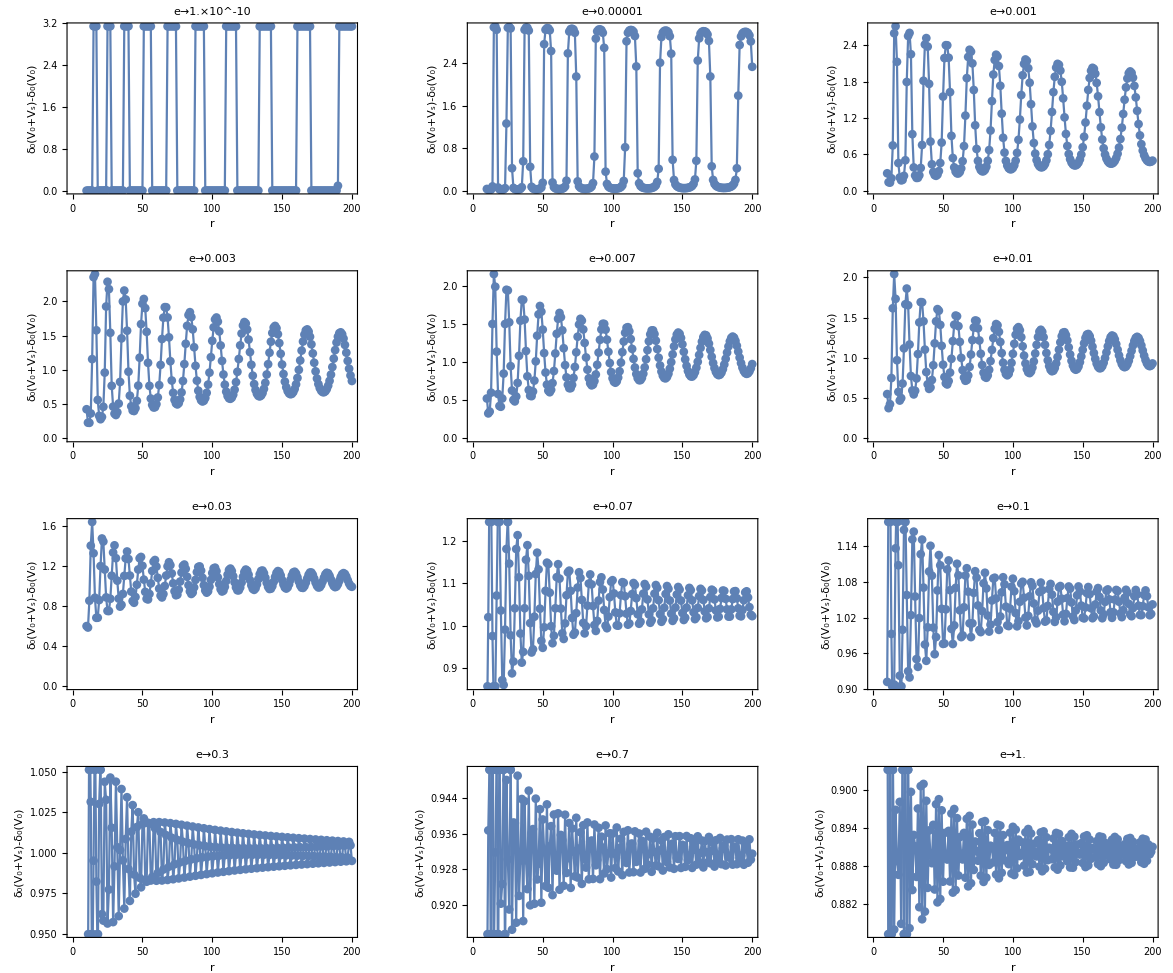

```mathematica
GraphicsGrid@Partition[ListPlot[δall[[#]],Frame->True,PlotLabel->"e"->N[ee[[#]],1],ImageSize->Medium,Axes->False,Joined->True,PlotMarkers->Automatic,AxesLabel->{"r","δ_0(V_0+V_s)-δ_0(V_0)"}]&/@Range@12,3]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_PhaseShift_minus.eps",%];
```

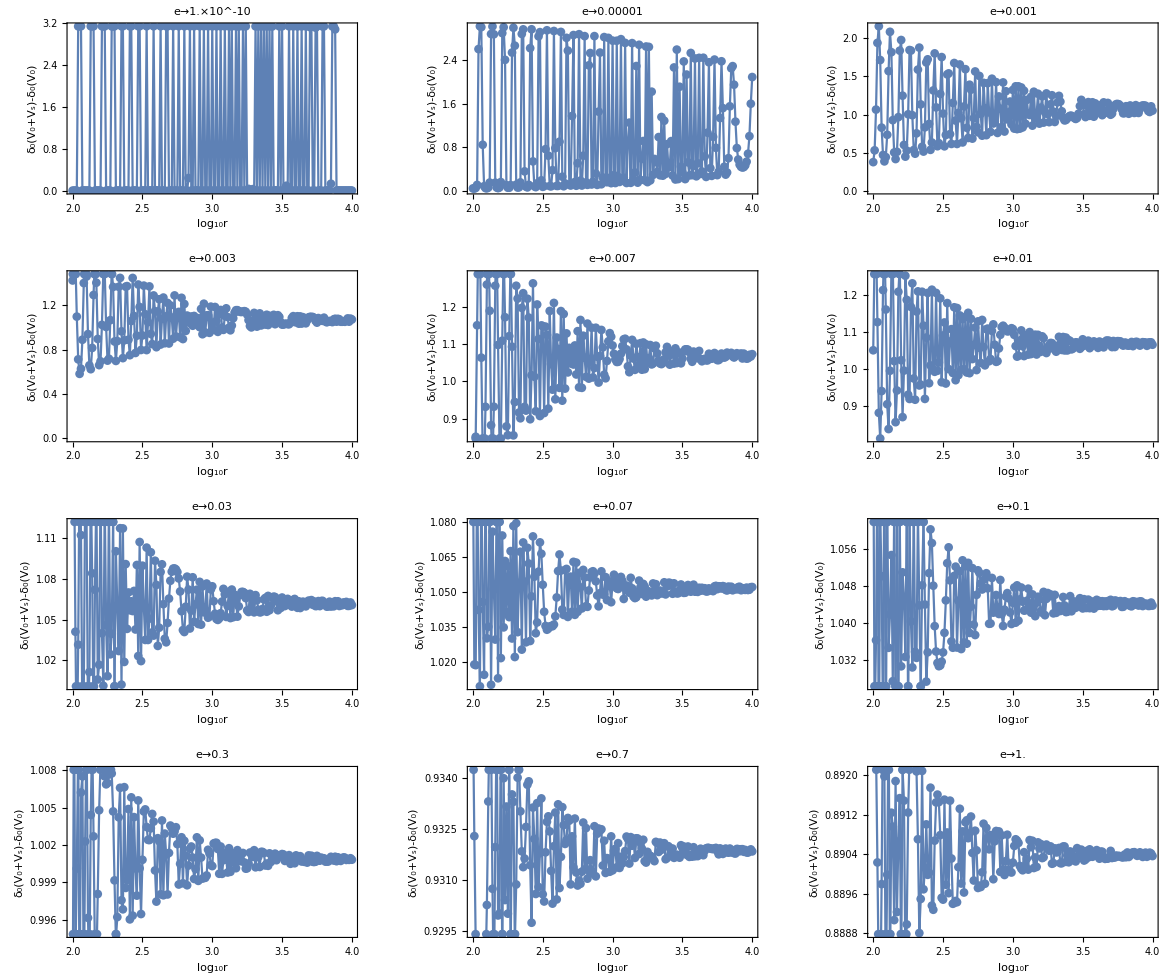

C:\Users\ASUS\OneDrive\文档\Test_6\Test_PhaseShift_minus_1.eps

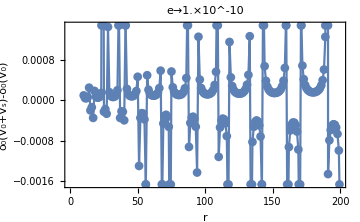
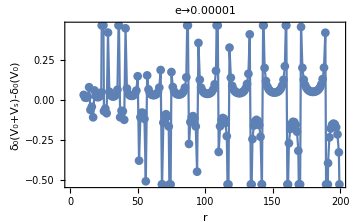
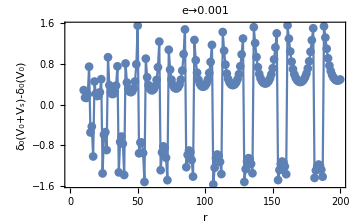
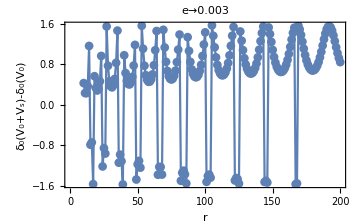
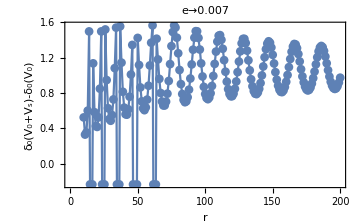
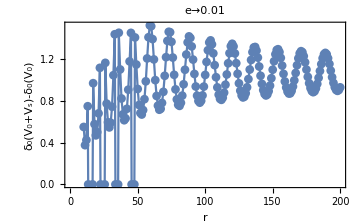
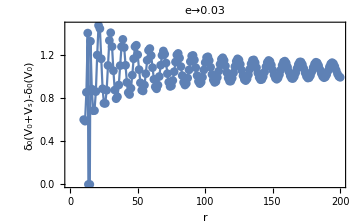
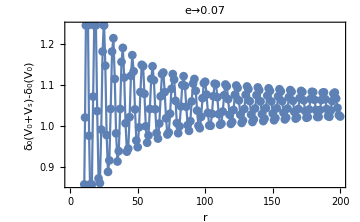

```mathematica
GraphicsGrid@Partition[ListPlot[δall1[[#]],Frame->True,PlotLabel->"e"->N[ee[[#]],1],ImageSize->Medium,Axes->False,Joined->True,PlotMarkers->Automatic,AxesLabel->{"log_10r","δ_0(V_0+V_s)-δ_0(V_0)"}]&/@Range@12,3]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_PhaseShift_minus_2.eps",%];
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

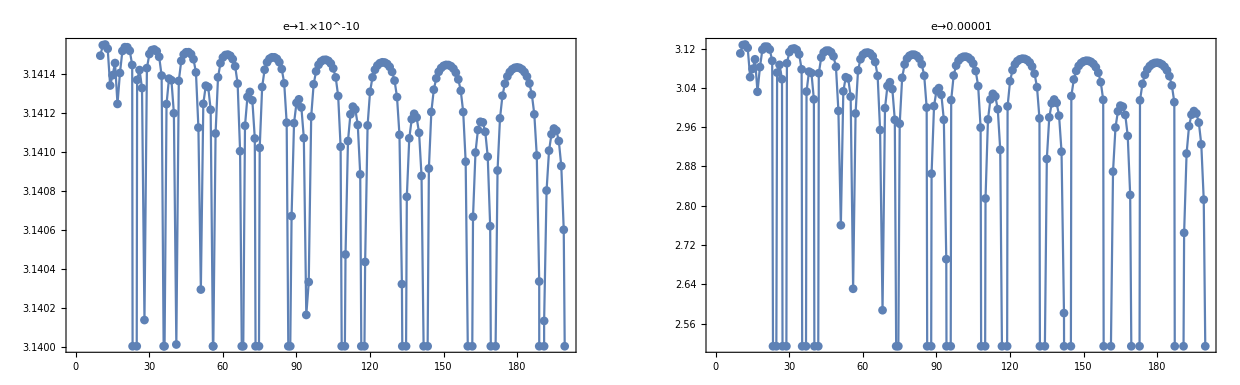

```mathematica
GraphicsGrid@Partition[Module[{δe,δδ,ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1},graph},
δδ=Flatten[Reap[Table[
δe=NestWhile[Sign[#-0.2](Abs[#]-π)&,#,!0.2<#<(0.2+π)&]&/@(δ[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&][r1,2]-δ[-1/#&][r1,2]);
Sow[{r1,δe[[#]]},ee[[#]]]&/@Range@2(*Sow[{r1,δe[[1]]},ee[[1]]];
Sow[{r1,δe[[2]]},ee[[2]]]*),{r1,10,200,1}],ee[[#]]&/@Range@2][[2]],1];
PrintTemporary[δδ[[#]]]&/@Range@2;
graph=ListPlot[δδ[[#]],Joined->True,Frame->True,PlotLabel->"e"->N[ee[[#]],1],PlotMarkers->Automatic,ImageSize->Large]&/@Range@2;PrintTemporary[graph];graph],2]
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.289222) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.511016) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.813081) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

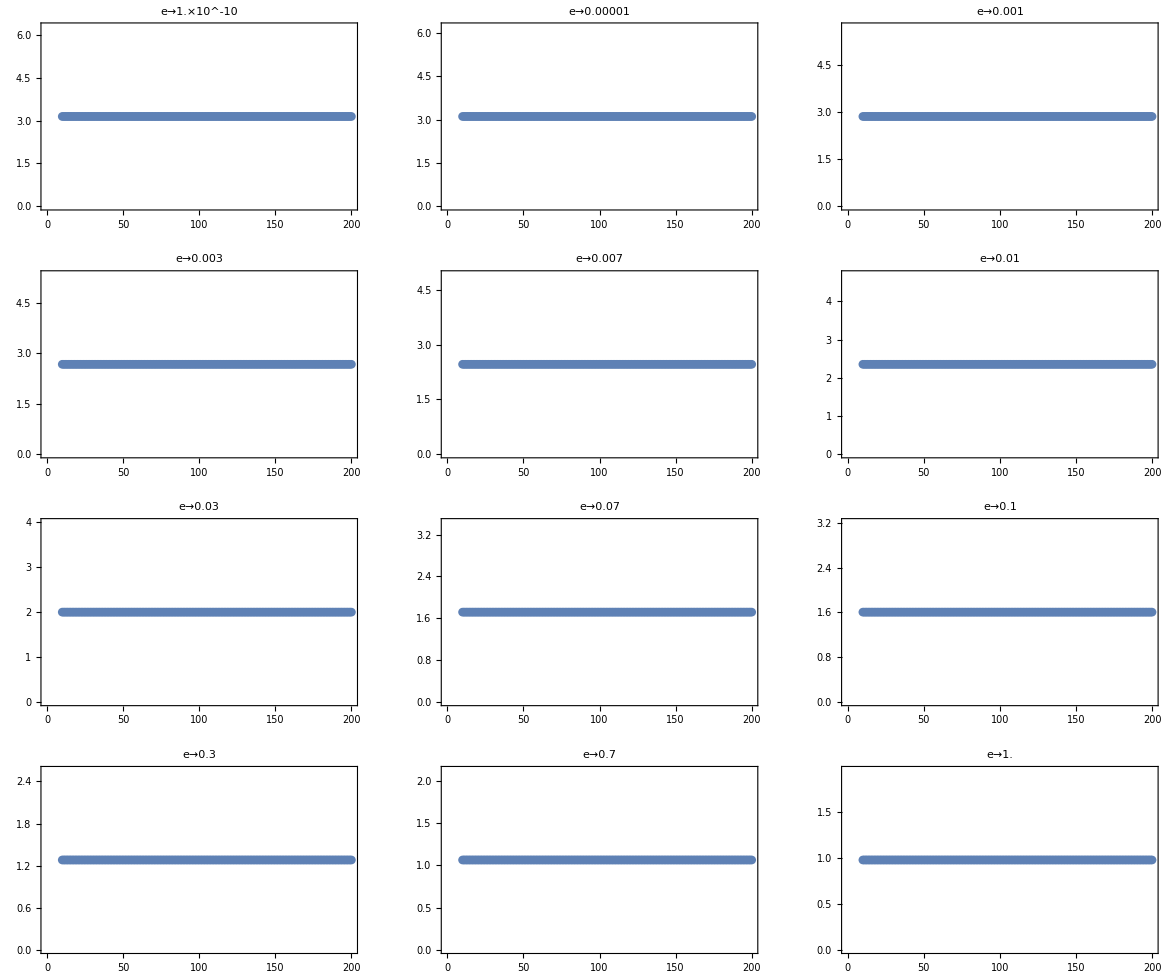

```mathematica
GraphicsGrid@Partition[Module[{δe,δδ,ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1},δmin=0,δmax},
δmax=δmin+π;
δδ=Flatten[Reap[Table[
δe=NestWhile[Sign[#-δmin](Abs[#]-π)&,#,!δmin<#<δmax&]&/@(δ[-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&][r1,12]);
Sow[{r1,δe[[#]]},ee[[#]]]&/@Range@12;
PrintTemporary[r1](*Sow[{r1,δe[[1]]},ee[[1]]];
Sow[{r1,δe[[2]]},ee[[2]]]*),{r1,10,200,1}],ee[[#]]&/@Range@12][[2]],1];
ListPlot[δδ[[#]],Joined->True,Frame->True,PlotLabel->"e"->N[ee[[#]],1],PlotMarkers->Automatic,ImageSize->Medium]&/@Range@12],3]
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.497182) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-1.01693) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-2.54928) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

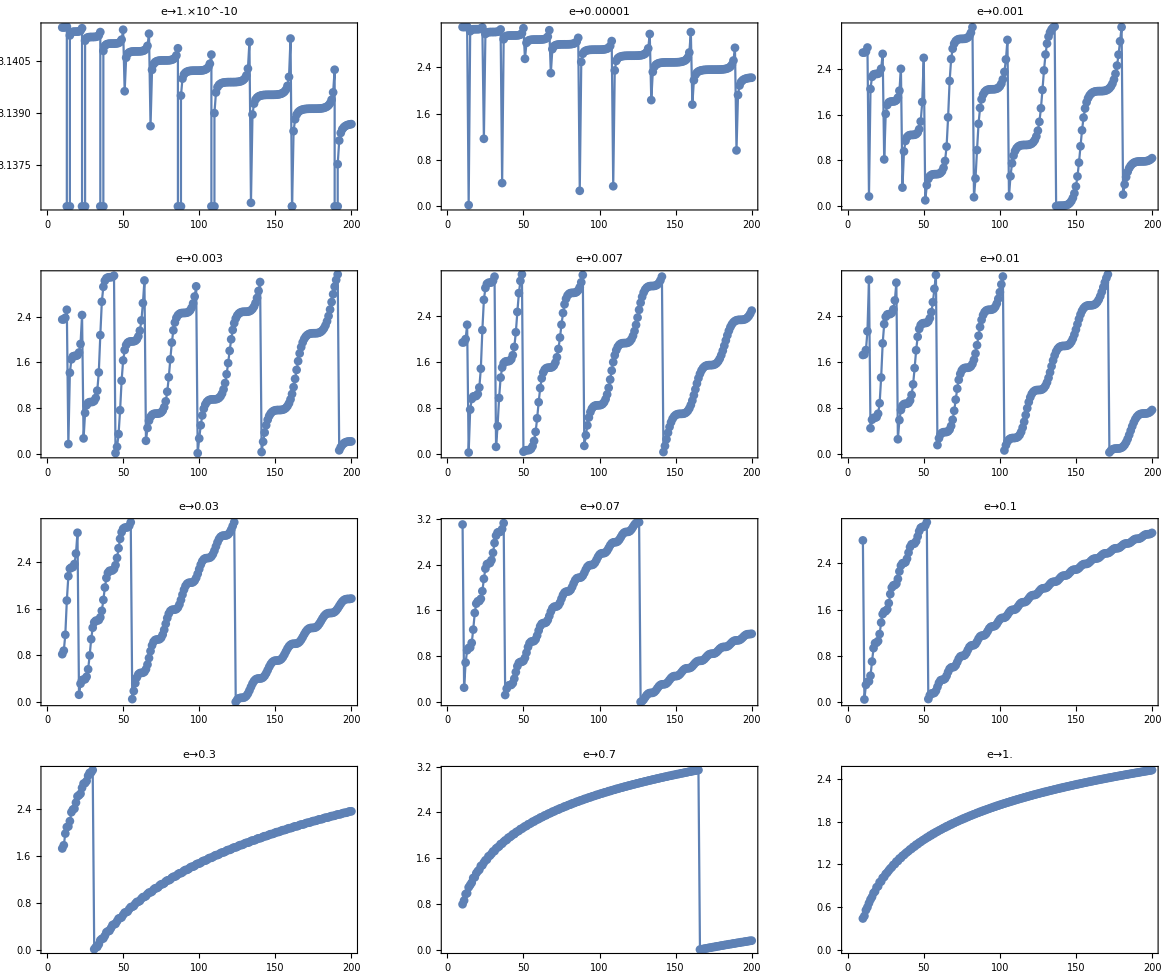

```mathematica
GraphicsGrid@Partition[Module[{δe,δδ,ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1},δmin=0,δmax},
δmax=δmin+π;
δδ=Flatten[Reap[Table[
δe=NestWhile[Sign[#-δmin](Abs[#]-π)&,#,!δmin<#<δmax&]&/@(δ[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&][r1,12]);
Sow[{r1,δe[[#]]},ee[[#]]]&/@Range@12;
PrintTemporary[r1](*Sow[{r1,δe[[1]]},ee[[1]]];
Sow[{r1,δe[[2]]},ee[[2]]]*),{r1,10,200,1}],ee[[#]]&/@Range@12][[2]],1];
ListPlot[δδ[[#]],Joined->True,Frame->True,PlotLabel->"e"->N[ee[[#]],1],PlotMarkers->Automatic,ImageSize->Medium]&/@Range@12],3]
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.92633) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-2.73449) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==6.67532) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

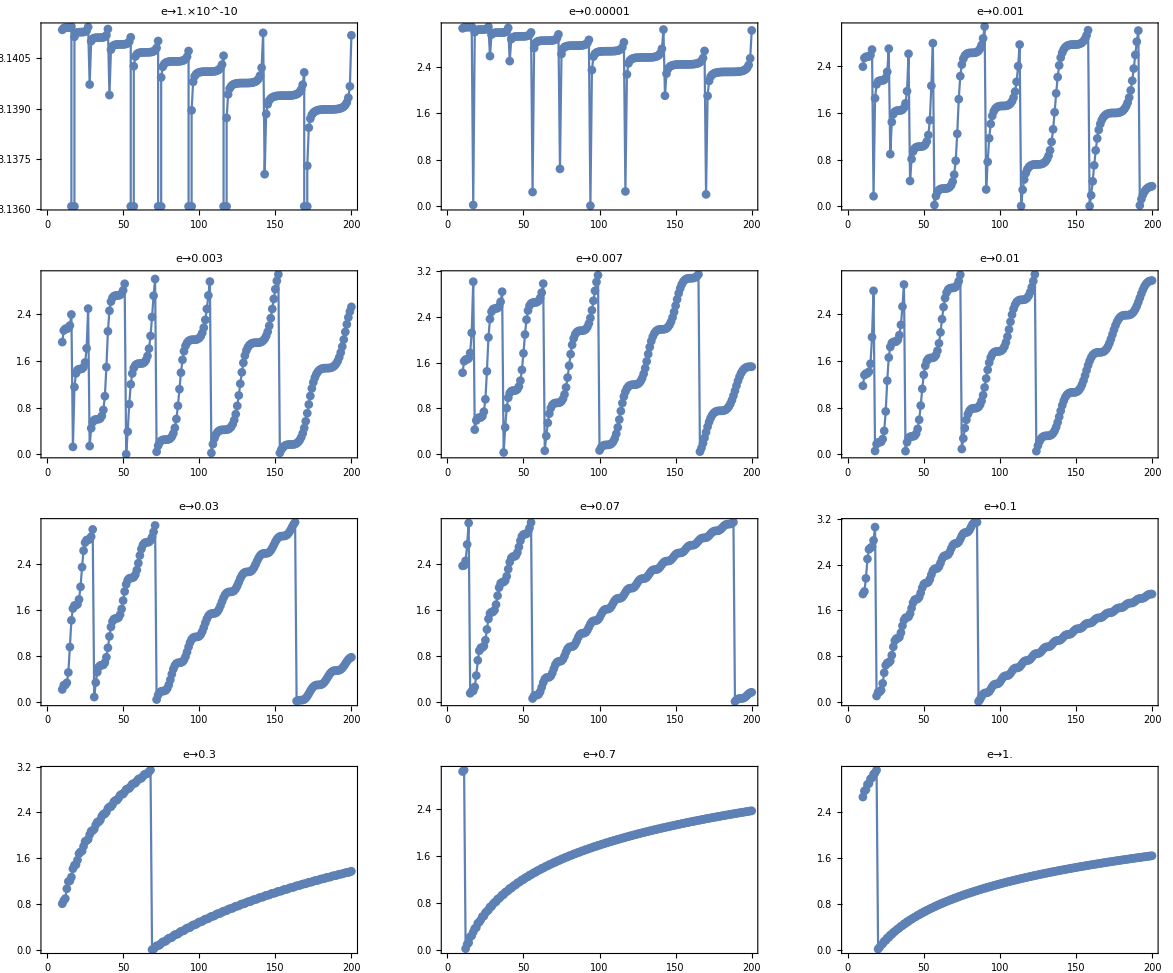

```mathematica
GraphicsGrid@Partition[Module[{δe,δδ,ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1},δmin=0,δmax},
δmax=δmin+π;
δδ=Flatten[Reap[Table[
δe=NestWhile[Sign[#-δmin](Abs[#]-π)&,#,!δmin<#<δmax&]&/@(δ[-1/#&][r1,12]);
Sow[{r1,δe[[#]]},ee[[#]]]&/@Range@12;
PrintTemporary[r1](*Sow[{r1,δe[[1]]},ee[[1]]];
Sow[{r1,δe[[2]]},ee[[2]]]*),{r1,10,200,1}],ee[[#]]&/@Range@12][[2]],1];
ListPlot[δδ[[#]],Joined->True,Frame->True,PlotLabel->"e"->N[ee[[#]],1],PlotMarkers->Automatic,ImageSize->Medium]&/@Range@12],3]
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.497182) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-1.01693) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-2.54928) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

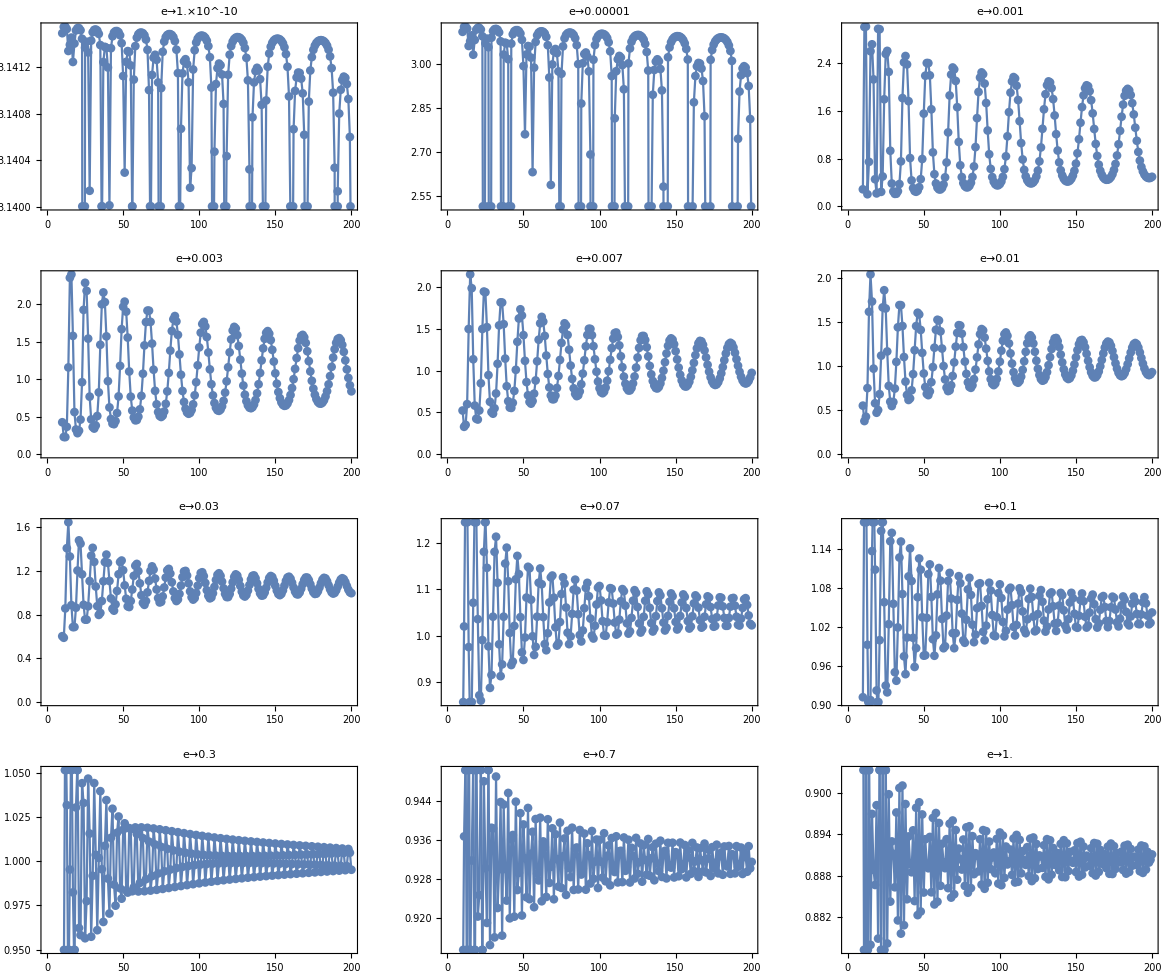

```mathematica
GraphicsGrid@Partition[Module[{δe,δδ,ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1},δmin=0.2,δmax},
δmax=δmin+π;
δδ=Flatten[Reap[Table[
δe=NestWhile[Sign[#-δmin](Abs[#]-π)&,#,!δmin<#<δmax&]&/@(δ[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&][r1,12]-δ[-1/#&][r1,12]);
Sow[{r1,δe[[#]]},ee[[#]]]&/@Range@12;
PrintTemporary[r1](*Sow[{r1,δe[[1]]},ee[[1]]];
Sow[{r1,δe[[2]]},ee[[2]]]*),{r1,10,200,1}],ee[[#]]&/@Range@12][[2]],1];
ListPlot[δδ[[#]],Joined->True,Frame->True,PlotLabel->"e"->N[ee[[#]],1],PlotMarkers->Automatic,ImageSize->Medium]&/@Range@12],3]
```

```mathematica
NestWhile[Sign[#-0.1](Abs[#]-π)&,#,!0.1<#<(0.1+π)&]&/@(δ[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&][50,1]-δ[-1/#&][50,1])
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

{3.1411249342394870878715065542705}